Radiation pressure + back-action evasion for nondegenerate internal squeezing

Attempt 1: Using Hamiltonian from Li et al, 2020

```mathematica
(*the code in this cell is from Xiang Li by personal correspondence, it is NOT my original work and my GitHub licence does not apply to it! -- James Gardner
g is ωs=κ and G is χ*)
solnsc=Solve[{
-I Ω A1==-γ A1 +Sqrt[2 γ]u1,
-I Ω A2 == -α/ℏ (X- L h)-γ A2 +Sqrt[2 γ]u2,
-I Ω X ==P/(M/4),
-I Ω P ==α A1},{A1,A2,X,P}];
v2outsc=u2-Sqrt[2γ]A2/.solnsc[[1]]//Simplify;
noise21sc=Coefficient[v2outsc,u1]//Simplify;
noise22sc=Coefficient[v2outsc,u2]//Simplify;
sigsc=Coefficient[v2outsc,h]//Simplify;
screp={γ->2 Pi 500.,ω0->2 Pi 3 10^8/(2 10^-6),ℏ->10^-34,Ω->2 Pi f,Pc->3 10^6,L->4000,c ->3 10^8,M->200};
qnoisesc=Sqrt[Abs[noise21sc]^2+Abs[noise22sc]^2]/Abs[sigsc]/.α->Sqrt[2Pc ℏ ω0/(L c)]/.screp;
hsql=Sqrt[8ℏ/(M Ω^2 L^2)]/.screp;

soln=Solve[{
-I Ω B1== G C1 +Sqrt[2 γ] u1+ g A1 -(γ) B1,
-I Ω B2== - G C2  +Sqrt[2 γ] u2+g A2 -(γ) B2,
-I Ω C1 ==-γm C1+ G B1+Sqrt[2 γm] fc1,
-I Ω C2 ==-γm C2-G B2+Sqrt[2 γm] fc2,
-I Ω A1==- g B1,
-I Ω A2 == -g B2-α/ℏ (X- L h),
-I Ω X ==P/(M/4),
-I Ω P ==α A1},{A1,A2,B1,B2,C1,C2,X,P}];
v2out=u2-Sqrt[2γ]B2/.soln[[1]];
(*The WLC parts include:quantum noise only,thermal noise,and combined.*)
noise21=Coefficient[v2out,u1]//Simplify;
noise22=Coefficient[v2out,u2]//Simplify;
noise2t1=Coefficient[v2out,fc1]Sqrt[2kB Tenv/(ℏ ωm)]//Simplify;
noise2t2=Coefficient[v2out,fc2]Sqrt[2kB Tenv/(ℏ ωm)]//Simplify;
sig=Coefficient[v2out,h]//Simplify;
wlcrep={g->2 Pi 5000(*6000*),G->2 Pi 4930(*5950*),γ->2 Pi 500.,γm->2 Pi 10^8/( 2 8 10^9),ωm->2 Pi  10^8,ω0->2 Pi 3 10^8/(2 10^-6),ℏ->10^-34,Tenv->4,kB->1.38 10^-23,Ω->2 Pi f,Pc->3 10^6,L->4000,c ->3 10^8,M->200};
(*qnoisebase=Sqrt[Abs[noise21]^2+Abs[noise22]^2]/Abs[sig]/.α->Sqrt[2Pc ℏ ω0/(L c)]/.baserep;*)
qnoisewlc=Sqrt[Abs[noise21]^2+Abs[noise22]^2]/Abs[sig]/.α->Sqrt[2Pc ℏ ω0/(L c)]/.wlcrep;
thnoisewlc=Sqrt[Abs[noise2t1]^2+Abs[noise2t2]^2]/Abs[sig]/.α->Sqrt[2Pc ℏ ω0/(L c)]/.wlcrep;
totalnoisewlc=Sqrt[Abs[noise21]^2+Abs[noise22]^2+Abs[noise2t1]^2+Abs[noise2t2]^2]/Abs[sig]/.α->Sqrt[2Pc ℏ ω0/(L c)]/.wlcrep;
hsql=Sqrt[8ℏ/(M Ω^2 L^2)]/.wlcrep;

(*clear all variables except for Li's functions*)
Clear@@DeleteCases[Names@"`*","hsql"|"qnoisesc"|"qnoisewlc"|"totalnoisewlc"];
```

```mathematica
(*setting global assumptions*)
$Assumptions={Ω≥0,γa≥0,γbtot≥γR>0,γc≥0,1>Rpd≥0,χ≥0,ωs>0,β∈Reals,ρRP≥0,ρBAE≥0,αOG∈Reals,ϕ∈Reals};
(*where β=(αGW Larm)/(2^(1/2)ℏ), ρRP=ρBAE=αGW^2/(2^(1/2)ℏ μ);*)

Id=IdentityMatrix[2];
(*simplifying upstream to better the end result*)
Ma=(γa-ⅈ Ω)Id+(ⅈ ρRP)/(2^(1/2)Ω^2)({{1, 1}, {-1, -1}});
invMa=Inverse[Ma]//Simplify;
Mc=(γc-ⅈ Ω)Id-(ⅈ ρBAE)/(2^(1/2)Ω^2)({{1, 1}, {-1, -1}});
invMc=Inverse[Mc]//Simplify;
Mb=(γbtot-ⅈ Ω)Id+ωs^2 Inverse[Ma]-χ^2({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}}).Inverse[Mc].({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}});(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
TimeConstraint0={0.1,1};
invMb=Simplify[Inverse[Mb],TimeConstraint->TimeConstraint0];

Γ=1/2^(1/2)({{1, 1}, {-ⅈ, ⅈ}});
Rin=Simplify[((1-Rpd)^(1/2)Γ.(Id-2 γR invMb).Inverse[Γ]),TimeConstraint->TimeConstraint0];
Rb=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)(2 (γbtot-γR))^(1/2)Γ. invMb.Inverse[Γ]),TimeConstraint->TimeConstraint0];
Ra=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)ωs (2 γa)^(1/2)Γ. invMb.invMa.Inverse[Γ]),TimeConstraint->TimeConstraint0];
Rc=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)(-χ)(2 γc)^(1/2)Γ.invMb.({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}}).invMc.Inverse[Γ]),TimeConstraint->TimeConstraint0];(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
T=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)ωs (-ⅈ β)Γ. invMb.invMa.({{1, 0}, {0, -1}})),TimeConstraint->TimeConstraint0];

(*theorem: conjugation commutes with any holomorphic function that is real-valued on the reals, which is all the functions we care about (check this!), use FlipI only if all variables are real*)
(*look at //FullForm, ⅈ is not present in all forms, sometimes is just Complex[0,1]*)
(*:> is RuleDelayed: "represents a rule that transforms lhs to rhs, evaluating rhs only after the rule is used. "*)
FlipI={ⅈ->-ⅈ,Complex[RePart_,ImPart_]->Complex[RePart,-ImPart]};
(*FlipI should catch all cases (check this with FullForm?, how? --> will not work through Hold, so don't use that)*)
ConjugateFlipI=Conjugate[f_]:>(f/.FlipI);
Sx=Simplify[(
Rpd Id
+Rin.ConjugateTranspose[Rin]
+Ra.ConjugateTranspose[Ra]
+Rb.ConjugateTranspose[Rb]
+Rc.ConjugateTranspose[Rc])/.ConjugateFlipI,TimeConstraint->{1,5}];
(*signal transfer function is Subscript[X, PD,2] wrt h not (X⃗)_PD wrt h⃗ --> factor of two from Subscript[(T.({{1}, {1}})), 22] versus Subscript[T, 22]
NB: another subtlety in that Subscript[T, 21]=Subscript[T, 22], but I don't know if this can be known a priori*)
sigTransfer = Simplify[(T.({{1}, {1}}))[[2]][[1]],TimeConstraint->{1,5}];(*[[1]] to remove atomic brackets {...}*)
sigTransferAbs= Simplify[ComplexExpand[Abs[sigTransfer]],TimeConstraint->{1,5}];
Sh=Simplify[Sx[[2,2]]/sigTransferAbs^2,TimeConstraint->{1,5}];
```

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 1. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
(*signal transfer function -- demonstration of factor of two*)
FullSimplify[(T.({{1}, {1}}))[[2]][[1]]/.{ρRP->0,ρBAE->0,Rpd->0,γa->0,γbtot->γR,γc->0,β->-αOG,ϕ->π/2}];
FullSimplify[(T.ConjugateTranspose[T])[[2,2]]/.{ρRP->0,ρBAE->0,Rpd->0,γa->0,γbtot->γR,γc->0,β->-αOG,ϕ->π/2}];
Print["sig. transfer fn.: ",Simplify[ComplexExpand[Abs[%%]^2]]," vs ", %]
```

sig. transfer fn.: (4 αOG^2 γR ωs^2)/(γR^2 Ω^2+(χ^2+Ω^2-ωs^2)^2) vs (2 αOG^2 γR ωs^2)/(γR^2 Ω^2+(χ^2+Ω^2-ωs^2)^2)

```mathematica
(*R.P. turned off, but lossy:
does it reduce to lossy sWLC? yes!*)
Simplify[Sh/.{ρRP->0,ρBAE->0,β->-αOG,ϕ->π/2}/.ConjugateFlipI,TimeConstraint->{1,5}];
(*comparing to (ASDShsWLC)^2 from sWLC.nb*)
PSDShsWLC=1/((γc^2+Ω^2)4 αOG^2 ωs^2 γR)(
((γbtot-2γR)(γa γc-Ω^2)-(γa+γc)Ω^2+ωs^2 γc-χ^2 γa)^2
+Ω^2(χ^2-ωs^2-(γbtot-2γR)(γa+γc)-γa γc+Ω^2)^2
+4γR γa ωs^2(γc^2+Ω^2)
+4γR γb(γa^2+Ω^2)(γc^2+Ω^2)
+4γR γc χ^2(γa^2+Ω^2)
+Rpd/(1-Rpd)((γbtot(γa γc-Ω^2)-(γa+γc)Ω^2+ωs^2 γc-χ^2 γa)^2
+Ω^2(χ^2-ωs^2-γbtot(γa+γc)-γa γc+Ω^2)^2));
(PSDShsWLC/.{γb->γbtot-γR})//FullSimplify
Print["Rad. pressure off, Sh reduces to lossy sWLC: ",ComplexExpand[%%%==%]//Simplify]
```

-1/(4 (-1+Rpd) αOG^2 γR (γc^2+Ω^2) ωs^2)((γa^2+Ω^2) (-2 γbtot γc χ^2-8 (-1+Rpd) γc γR χ^2+γc^2 Ω^2+γbtot^2 (γc^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)

Rad. pressure off, Sh reduces to lossy sWLC: True

```mathematica
(*want to show that Sx reduces to lossy sWLC (in order to inspect the denom),
simplfying assuming ϕ=π/2, have to start further back because simplifying Sx takes too long
--> i.e. applying Sx[[2,2]]/.ConjugateRepl just hangs, so use ConjugateFlipI*)
(*all variables are real, so tell .nb to expand conjugates just based on ⅈ*)
Sx022=Together[Sx[[2,2]]/.ϕ->π/2];
Sx022num=Collect[Numerator[Sx022]//Expand,{ρRP,ρBAE},FullSimplify]
Sx022denom=Denominator[Sx022]//Expand//FullSimplify
(*check that manipulation hasn't changed anything*)
Sx022==Sx022num/Sx022denom//Simplify
(*showing that poles are preserved, denom is similar enough
--> therefore stability is the same and pole-defined threshold values are the same*)
prevDenom=((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4);
(Sx022denom==Ω^4 prevDenom^2)//Simplify
(*for completeness, should show this for ϕ free but this will be tedious and should follow anyway*)
```

-8 (-1+Rpd) γR ρRP^2 (γc^2+Ω^2) ωs^2 (γa ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)+(γc χ^2+γbtot (γc^2+Ω^2)) ωs^2)-8 (-1+Rpd) γR ρBAE^2 χ^2 (γa^2+Ω^2) ((γa^2+Ω^2) (γbtot (γbtot γc+χ^2)+γc Ω^2)+(γa (2 γbtot γc+χ^2)-2 γc Ω^2) ωs^2+γc ωs^4)+Ω^4 ((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4) ((γa^2+Ω^2) (-2 γbtot γc χ^2-8 (-1+Rpd) γc γR χ^2+γc^2 Ω^2+γbtot^2 (γc^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)+16 (-1+Rpd) γR ρBAE ρRP χ^2 ωs^2 (γa Ω^2 (4 γbtot γc-3 γc^2+χ^2+Ω^2)+γa^2 γc (γbtot γc+χ^2+3 Ω^2)+γa γc^2 ωs^2+Ω^2 (γbtot (-2 γc^2+Ω^2)+γc (-Ω^2+ωs^2)))

Ω^4 ((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)^2

True

True

```mathematica
(*signal transfer function is indep of RP and BAE and its denominator is exactly that from before,
NB: this is for the h (not h⃗) defintion, exactly what the h⃗ definition would be is unclear
--> the key difference between noise and signal is that for the noise the inputs are uncorrelated quadratures but for the signal the input is correlated h⃗, we could do everything wrt Subscript[X, 1,h] instead (where Subscript[X, 2,h]=0) which would yield the same result up to factors of 2*)
Block[{ϕ=π/2},
T0=Together[sigTransferAbs^2//Simplify]]
Denominator[T0]//FullSimplify
%==prevDenom
```

-((4 (-1+Rpd) β^2 γR (γc^2+Ω^2) ωs^2)/(γa^2 γbtot^2 γc^2-2 γa^2 γbtot γc χ^2+γa^2 χ^4+γa^2 γbtot^2 Ω^2+γa^2 γc^2 Ω^2+γbtot^2 γc^2 Ω^2+2 γa^2 χ^2 Ω^2-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γa^2 Ω^4+γbtot^2 Ω^4+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+2 γa γbtot γc^2 ωs^2-2 γa γc χ^2 ωs^2+2 γa γbtot Ω^2 ωs^2-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+γc^2 ωs^4+Ω^2 ωs^4))

(γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4

True

```mathematica
-((4 (-1+Rpd) β^2 γR (γc^2+Ω^2) ωs^2)/(γa^2 γbtot^2 γc^2-2 γa^2 γbtot γc χ^2+γa^2 χ^4+γa^2 γbtot^2 Ω^2+γa^2 γc^2 Ω^2+γbtot^2 γc^2 Ω^2+2 γa^2 χ^2 Ω^2-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γa^2 Ω^4+γbtot^2 Ω^4+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+2 γa γbtot γc^2 ωs^2-2 γa γc χ^2 ωs^2+2 γa γbtot Ω^2 ωs^2-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+γc^2 ωs^4+Ω^2 ωs^4))
```

-((4 (-1+Rpd) β^2 γR (γc^2+Ω^2) ωs^2)/(γa^2 γbtot^2 γc^2-2 γa^2 γbtot γc χ^2+γa^2 χ^4+γa^2 γbtot^2 Ω^2+γa^2 γc^2 Ω^2+γbtot^2 γc^2 Ω^2+2 γa^2 χ^2 Ω^2-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γa^2 Ω^4+γbtot^2 Ω^4+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+2 γa γbtot γc^2 ωs^2-2 γa γc χ^2 ωs^2+2 γa γbtot Ω^2 ωs^2-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+γc^2 ωs^4+Ω^2 ωs^4))

```mathematica
(*simplifying equation for investigating BAE for ϕ≠±π/2, first: signal transfer function*)
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&;
Block[{sigT=Together[sigTransferAbs]},
numerT=Numerator[sigT];
denomT=Denominator[sigT];
(*sanity check
Print[numerT/denomT==Together[sigTransferAbs]];-->True*)]
(*notice that signal transfer function only changes if ϕ≠±π/2 and Subscript[ρ, BAE]≠0*)
numerTsqr=Collect[numerT^2,{ϕ,ρRP,ρBAE},SimplifyConstrained]
denomTsqr=Collect[denomT^2,{ϕ,ρRP,ρBAE},SimplifyConstrained]
sigTsqrSimpl=numerTsqr/denomTsqr;
(*sanity check
Simplify[numerTsqr==Numerator[Together[sigTransferAbs^2]]]
Simplify[denomTsqr==Denominator[Together[sigTransferAbs^2]]]
--> True True*)
(*Sx22===1+((...)+[complicated])/((…)+(…)ρRP ρBAE Cos[ϕ]^2+(…)(ρRP ρBAE Cos[ϕ]^2)^2);
sigTransferAbs^2===((…)+(…)ρRP ρBAE Sin[2ϕ]^2+(…)(ρRP ρBAE Sin[2ϕ]^2)^2)/((…)+(…)ρRP ρBAE Cos[ϕ]^2+(…)(ρRP ρBAE Cos[ϕ]^2)^2);*)

(*investigating BAE for ϕ≠±π/2, second: noise transfer function:
let ΔSx=Sx22-1 s.t. Sx11 = 1 + ΔSx
--> first problem is dealing with Conjugates in Sx22, which is now far faster due to ConjugateFlipI working on Sx for less than 5% of a second*)
Block[{
noiseΔSx=Together[Sx[[2,2]]-1],
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&},
numerΔSx=Collect[Numerator[noiseΔSx],{ϕ,ρRP,ρBAE},SimplifyConstrained];
denomΔSx=Collect[Denominator[noiseΔSx],{ϕ,ρRP,ρBAE},SimplifyConstrained];]
(*want to show that Sx is demonstrably real*)
(*common factor Exp[4ⅈ ϕ] accrued in numerator and denominator, cancel explictly --> formula is demonstrably real*)
commonFactor0=Exp[-4ⅈ ϕ];
numerΔSxSimpl=Collect[(commonFactor0 numerΔSx)//ExpToTrig,{ϕ,ρRP,ρBAE},SimplifyConstrained]/.(ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(4 ⅈ ϕ)))->2ⅈ Sin[2ϕ]
denomΔSxSimpl=Collect[(commonFactor0 denomΔSx)//ExpToTrig,{ϕ,ρRP,ρBAE},SimplifyConstrained]
Print["same denom. as signal transfer fn?: ",denomTsqr==denomΔSxSimpl]
SxSimpl=1+numerΔSxSimpl/denomΔSxSimpl;

(*Sh=SxSimpl/sigTsqrSimpl=(1+numerΔSxSimpl/denomΔSxSimpl)/(numerTsqr/denomTsqr)*)
ShSimpl=Simplify[(denomΔSxSimpl+numerΔSxSimpl)/numerTsqr,TimeConstraint->{0.1,1}];
```

16 β^2 (γR-Rpd γR) Ω^8 (γc^2+Ω^2) ωs^2 ((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)-16 √2 β^2 (γR-Rpd γR) ρBAE χ^2 Ω^6 ωs^2 ((γa^2+Ω^2) (γbtot (-γc^2+Ω^2)+γc (χ^2+2 Ω^2))+(-γa γc^2+(γa-2 γc) Ω^2) ωs^2) Sin[2 ϕ]-8 (-1+Rpd) β^2 γR ρBAE^2 χ^4 Ω^4 (γa^2+Ω^2) ωs^2 Sin[2 ϕ]^2

4 Ω^8 ((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)^2+16 ρBAE ρRP χ^2 Ω^4 ωs^2 (Ω (χ^2-γc Ω+Ω^2-γbtot (γc+Ω))-γa (χ^2+γbtot (-γc+Ω)+Ω (γc+Ω))+(γc-Ω) ωs^2) (γbtot Ω (-γc+Ω)+γa (χ^2-γc Ω+Ω^2-γbtot (γc+Ω))+Ω (χ^2+Ω (γc+Ω))-(γc+Ω) ωs^2) Cos[ϕ]^2+16 ρBAE^2 ρRP^2 χ^4 ωs^4 Cos[ϕ]^4

FullSimplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of FullSimplify::time will be suppressed during this calculation.

FullSimplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

FullSimplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

FullSimplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

FullSimplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of FullSimplify::time will be suppressed during this calculation.

FullSimplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

32 (-1+Rpd) γc γR χ^2 Ω^8 (γa^2+Ω^2) (-(γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)+2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2-(γc^2+Ω^2) ωs^4)-32 (-1+Rpd) γR ρBAE^2 χ^2 Ω^4 (γa^2+Ω^2) ((γa^2+Ω^2) (γbtot (γbtot γc+χ^2)+γc Ω^2)+(γa (2 γbtot γc+χ^2)-2 γc Ω^2) ωs^2+γc ωs^4) Sin[ϕ]^2+8 √2 (-1+Rpd) γR ρBAE χ^2 Ω^6 (γa^2+Ω^2) ((γa^2+Ω^2) (2 γbtot γc χ^2-3 γc^2 Ω^2+γbtot^2 (-3 γc^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γc (3 γbtot γc-χ^2)+(-γa γbtot-3 γc^2+χ^2) Ω^2+Ω^4) ωs^2+(-3 γc^2+Ω^2) ωs^4) Sin[2 ϕ]+ρRP^2 (-32 (-1+Rpd) γR Ω^4 (γc^2+Ω^2) ωs^2 (γa ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)+(γc χ^2+γbtot (γc^2+Ω^2)) ωs^2)+32 (-1+Rpd) γR ρBAE^2 χ^2 ωs^2 Cos[ϕ]^2 (-γa χ^2-2 γc ωs^2+γa χ^2 Cos[2 ϕ])+32 √2 (-1+Rpd) γR ρBAE χ^2 Ω^2 ωs^2 (γa γbtot (-γc^2+Ω^2)+γa γc (χ^2+2 Ω^2)+γc^2 ωs^2) Sin[2 ϕ])+ρRP (-16 (-1+Rpd) γR ρBAE χ^2 Ω^4 ωs^2 (-16 γa γbtot γc Ω^2+γa^2 (γbtot (γc-Ω) (γc+Ω)-5 γc (χ^2+2 Ω^2))+γa (γc-Ω) (γc+Ω) ωs^2+Ω^2 (γbtot (γc-Ω) (γc+Ω)+3 γc (χ^2+2 (Ω-ωs) (Ω+ωs)))+(γa^2 (γc (5 γbtot γc-χ^2)-(γbtot-2 γc) Ω^2)+Ω^2 (-7 γbtot γc^2+3 γc χ^2+3 γbtot Ω^2+2 γc Ω^2-2 γc ωs^2)+γa (4 Ω^2 (-3 γc^2+χ^2+Ω^2)+(5 γc^2-Ω^2) ωs^2)) Cos[2 ϕ])+8 √2 (-1+Rpd) γR ρBAE^2 χ^2 Ω^2 ωs^2 (-γa^2 (4 γbtot γc+3 χ^2)+(4 γbtot γc+χ^2) Ω^2+γa γc (8 Ω^2-4 ωs^2)+χ^2 (γa^2+Ω^2) Cos[2 ϕ]) Sin[2 ϕ])

4 Ω^8 ((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)^2+16 ρBAE ρRP χ^2 Ω^4 ωs^2 (Ω (χ^2-γc Ω+Ω^2-γbtot (γc+Ω))-γa (χ^2+γbtot (-γc+Ω)+Ω (γc+Ω))+(γc-Ω) ωs^2) (γbtot Ω (-γc+Ω)+γa (χ^2-γc Ω+Ω^2-γbtot (γc+Ω))+Ω (χ^2+Ω (γc+Ω))-(γc+Ω) ωs^2) Cos[ϕ]^2+16 ρBAE^2 ρRP^2 χ^4 ωs^4 Cos[ϕ]^4

same denom. as signal transfer fn?: True

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
(*-------------------------------------------------------------------------------------------------------------------*)
SetDirectory[NotebookDirectory[]];

(*physical constants*)
c=3. 10^8(*ms^-1*);
ℏ=1. 10^-34(*Js*);

setDerivedParams1[]:=(
τRoundTripArm=(2 Larm)/c;
τRoundTripSRC=(2Lsrc)/c;
γR=-1/(2 τRoundTripSRC)Log[1-Tsrm];
(*an approximation when ωs<<ωFSR=1/τRoundTripArm*)
ωs=c(Titm/(4 Lsrc Larm))^(1/2);
(*using formula for G from Korobko*)(*rescaling of α by 1/(2^(1/2)ℏ) seems to be in Li?, chosen β s.t. turning R.P. off should match β=(αGW Larm)/(2^(1/2)ℏ), which is ((Pcirc Larm ω0)/(ℏ c))^(1/2) if αGW from Li is used --> factor of two missing? this is unresolved, but just use β=-G s.t. ahatdot=...+iGh or ...-iβh;
ρRP=ρBAE=αGW^2/(2^(1/2)ℏ μ)=(2^(1/2)ℏ β^2)/(Larm^2 μ); but |α|=|αGW Larm|*)
(*!changing now to use Li formula for comparison to sWLC, why do these two disagree? I do not know.*)
β=((Pcirc Larm ω0)/(ℏ c))^(1/2);
μ=M/4;
(*(2^(1/2)ℏ β^2)/(Larm^2 μ)*)
ρ=1/(2^(1/2)ℏ μ)(2 ℏ^2)/Larm^2 β^2;)

setConfigParamsCustom[λ00_,Larm0_,Lsrc0_,Pcirc0_,Titm0_,Tsrm0_,M0_,paramSetName0_:None,γR0_:None,ωs0_:None]:=(
Clear[paramSetName,λ0,Larm,Lsrc,Pcirc,Titm,Tsrm,M,τRoundTripArm,τRoundTripSRC,γR,ωs,β,μ,ρ];
(*manually set parameters, all in base SI units*)
paramSetName=If[paramSetName0===None,"Custom parameter set",paramSetName0];
λ0=λ00(*m*);ω0=2π c/λ0;
Larm=Larm0(*m*);
(*can be omitted if γR and Tsrm are specified*)
Lsrc=If[Lsrc0===None,Lsrc ,Lsrc0(*m*)];
Pcirc=Pcirc0(*W*);
(*can be omitted if ωs is specified*)
Titm=If[Titm0===None,Titm,Titm0];
Tsrm=Tsrm0;
M=M0(*kg*);
setDerivedParams1[];
(*if specified, then override γR and ωs*)
If[Not[γR0===None],γR=γR0];
If[Not[ωs0===None],ωs=ωs0];
(*if unspecified, then use γR and Tsrm to find τRoundTripSRC*)
If[Lsrc0===None,τRoundTripSRC=-1/(2 γR)Log[1-Tsrm]
(*Print["inferred Lsrc (in m) = ",c τRoundTripSRC/2,"\n"];*);];
(*!changing now to use Li formula for comparison to sWLC, why do these two disagree? I do not know.*)
β=((Pcirc Larm ω0)/(ℏ c))^(1/2);
μ=M/4;
ρ=1/(2^(1/2)ℏ μ)(2 ℏ^2)/Larm^2 β^2(*=(2^(1/2)ℏ β^2)/(Larm^2 μ)*);)

(*different interferometer parameter sets*)
(*λ0,Larm,Lsrc,Pcirc,Titm,Tsrm,M, optional: paramSetName,γR,ωs*)
(*parameters of Advanced LIGO, from Adya et al, 2020 and https://dcc.ligo.org/public/0000/T0900043/011/LIGO-T0900043-11.pdf*)
setConfigParamsALIGO[]:=setConfigParamsCustom[1064. 10^-9(*m*),4. 10^3(*m*),56.(*m*),750. 10^3 (*W*),0.014,0.325,40.(*kg*),"Advanced LIGO"]

(*parameters of LIGO Voyager, from Adhikari et al, 2020*)
setConfigParamsVoyager[]:=setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),56.(*m*)(*I assume that the upgrade is not changing Lsrc, which is not made obvious anywhere*),3. 10^6 (*W*),0.002,0.046,200.(*kg*),"LIGO Voyager"]

(*parameters of NEMO, from Ackley et al, 2020*)
setConfigParamsNEMO[]:=setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),354.(*m*), 4.5 10^6(*W*),0.014,0.048,74.1(*kg*),"NEMO"]

(*parameters from Korobko et al, 2019: "benchmark 3rd generation detector"*)
setConfigParamsKorobko2019[]:=setConfigParamsCustom[1550. 10^-9(*m*),20. 10^3(*m*),56.(*m*),4. 10^6(*W*),0.07,0.35,200.(*kg*),"Korobko et al, 2019"]

(*parameters from Li et al, 2020 - NB:ωs and γR are not from LIGO Voyager!*)
setConfigParamsLi2020[γR0_:None]:=setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),None,3. 10^6(*W*),None,0.046(*assuming LIGO Voyager's Subscript[T, SRM] was used for γR*),200.(*kg*),"Li et al, 2020",If[γR0===None,2π 500.(*Hz*),γR0],2π 5000.(*Hz*)]

printParams[]:=Print[StringForm[
"configuration parameters:\nparamSetName=``, λ0=`` m, Larm=`` km, Lsrc=`` m, Pcirc=`` MW, Titm=``, Tsrm=``, M=`` kg\nderived parameters:\nωFSR/(2  π)=1/τRoundTripArm=`` kHz, 1/τRoundTripSRC=`` kHz, γR/(2  π)=`` kHz, ωs/(2  π)=`` kHz; ωs/γR=``",paramSetName,NumberForm[λ0],NumberForm[Larm 10^-3],NumberForm[Lsrc],NumberForm[Pcirc 10^-6],NumberForm[Titm],NumberForm[Tsrm],NumberForm[M],NumberForm[1/τRoundTripArm 10^-3,3],NumberForm[1/τRoundTripSRC 10^-3,3],NumberForm[γR/(2π)10^-3,3],NumberForm[ωs/(2π)10^-3,3],NumberForm[ωs/γR]]]
```

```mathematica
(*to-do: find experimental constraints:,
-- optical loss --> see Zhang,
-- maximum squeezing ratio to singularity threshold --> see Sheon, 0.95 and rule of thumb 0.7,*)
(*"realistic" losses, using those from Zhang et al, 2021 which seem to be pretty representative*)
Tla0=100. 10^-6(*=100ppm, arm cavity loss port*);
Tlb0=1000. 10^-6(*=1000ppm, signal SRC loss port*);
Tlc0=1000. 10^-6(*=1000ppm, idler SRC loss port*); (*along with symSRM=True as the default from now on*)
Rpd0=0.1(*=10%*);

Clear[singularityThr]
singularityThr[Tla_,Tlb_,Tlc_,symSRM_:True]:=(
poleSol0={{Ω->0,χ->√(γc (γbtot+ωs^2/γa))},{Ω->√((-γa^2 (γbtot+γc)-γa ωs^2+γc ωs^2)/(γbtot+γc)),χ->√((γa+γbtot) (γa+γc+ωs^2/(γbtot+γc)))}};

If[Tla≠0,Min[χ/.poleSol0/.{γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM]}],χ/.poleSol0[[2]]/.{γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM]}])

(*loss functions*)
γaFn[Tla_]:=-1/(2 τRoundTripArm)Log[1-Tla]
γbtotFn[Tlb_]:=γR+-1/(2 τRoundTripSRC)Log[1-Tlb]
γcFn[Tlc_,symSRM_:True]:=If[symSRM,γR+-1/(2 τRoundTripSRC)Log[1-Tlc],-1/(2 τRoundTripSRC)Log[1-Tlc]]
(*plotting sensitivity -- un-simplified Sh*)
(*taking real part to discard numerical error creating tiny imaginary parts*)
QNwRP[Ω0_?NumericQ,χ0_?NumericQ,ϕ0_?NumericQ,Tla_?NumericQ,Tlb_?NumericQ,Tlc_?NumericQ,Rpd0_?NumericQ,ρRPTrue_:True,ρBAETrue_:False,symSRM_:True]:=Re[Sqrt[SxSimpl]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
sigwRP[Ω0_?NumericQ,χ0_?NumericQ,ϕ0_?NumericQ,Tla_?NumericQ,Tlb_?NumericQ,Tlc_?NumericQ,Rpd0_?NumericQ,ρRPTrue_:True,ρBAETrue_:False,symSRM_:True]:=Re[Sqrt[sigTsqrSimpl]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
ASDShwRP[Ω0_?NumericQ,χ0_?NumericQ,ϕ0_?NumericQ,Tla_?NumericQ,Tlb_?NumericQ,Tlc_?NumericQ,Rpd0_?NumericQ,ρRPTrue_:True,ρBAETrue_:False,symSRM_:True]:=Re[Sqrt[ShSimpl]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}

(*to-do: pad out Tla, Tlb, Tlc to accommodate ppm and non ppm inputs*)
legendStyler[vals0_]:=(
(*pad out vals0 with default arguments of wRP functions*)
If[Length[vals0]==6,vals=Join[vals0,{True,False,True}],
If[Length[vals0]==7,vals=Join[vals0,{False,True}],
If[Length[vals0]==8,vals=Join[vals0,{True}],vals=vals0]]];
(*in order to evaluate any held singularity thresholds*)
vals=vals//ReleaseHold;
paddedStrings=
Join[StringPadRight[ToString[N[vals[[1]]/singularityThr[vals[[3]],vals[[4]],vals[[5]],vals[[9]]]]],4],StringPadRight[ToString[N[vals[[2]]/(2π)]],5],StringPadRight[ToString[N[If[vals[[3]]<0.01,vals[[3]] 10^6,vals[[3]]]]],5],StringPadRight[ToString[N[If[vals[[4]]<0.01,vals[[4]] 10^6,vals[[4]]]]],6],StringPadRight[ToString[N[If[vals[[5]]<0.01,vals[[5]] 10^6,vals[[5]]]]],6],StringPadRight[ToString[vals[[6]]],4]];
(*<> is StringJoin*)
Style[StringForm["χ/χThr=``, "<>ToString[If[Mod[vals[[2]]-π/2,π]==0,StringPadRight[ToString[StringForm["ϕ=``π/2",If[Mod[vals[[2]]-π/2,2π]==0,"+","-"]]],12],StringForm["ϕ/(2π)=``",
paddedStrings[[2]]]]]
<>If[vals[[3]]<0.01,"; T_(l, a)=``ppm","; T_(l, a)=``"]
<>If[vals[[4]]<0.01,", T_(l, b)=``ppm",", T_(l, b)=``"]
<>If[vals[[9]],
", γ_(c, tot)=γ_R+γ_c"<>If[vals[[5]]<0.01,"(T_(l, c)=``ppm)","(T_(l, c)=``)"],
If[vals[[5]]<0.01,", T_(l, c)=``ppm",", T_(l, c)=``"]]
<>", R_PD=``"
<>If[Not[vals[[7]]],"; no RP",""]
<>If[vals[[8]],"; with BAE",""],
paddedStrings[[1]],
paddedStrings[[3]],
paddedStrings[[4]],
paddedStrings[[5]],
paddedStrings[[6]]],
FontFamily->"Monospace"])
(*assumes that BAE and symSRM are turned off*)
legendStylerShort[vals0_]:=Style[StringForm["χ/χ_thr=``, T_(l, a)=``ppm, T_(l, b)=``ppm, T_(l, c)=``ppm, R_PD=``, ρ``",StringPadRight[ToString[NumberForm[(vals0[[1]]//ReleaseHold)/singularityThr[vals0[[3]],vals0[[4]],vals0[[5]],False],2]],4],NumberForm[N[vals0[[3]] 10^6]],NumberForm[N[vals0[[4]] 10^6]],NumberForm[N[vals0[[5]] 10^6]],NumberForm[N[vals0[[6]]]],If[vals0[[7]],"≠0","=0"]],FontFamily->"Monospace"]
legendStylerSplit[vals0_]:=Style[StringForm["χ/χ_thr=``, T_(l, a)=``ppm, T_(l, b)=``ppm,\nT_(l, c)=``ppm, R_PD=``, ρ``",StringPadRight[ToString[NumberForm[(vals0[[1]]//ReleaseHold)/singularityThr[vals0[[3]],vals0[[4]],vals0[[5]],False],2]],4],NumberForm[N[vals0[[3]] 10^6]],NumberForm[N[vals0[[4]] 10^6]],NumberForm[N[vals0[[5]] 10^6]],NumberForm[N[vals0[[6]]]],If[vals0[[7]],"≠0","=0"]],FontFamily->"Monospace"]

plotwRP[valsList_,plotLabel_:None,plotStyle_:{},fRange_:{10,10^4}]:=(
{fmin,fmax}=fRange;
p1=LogLinearPlot[Evaluate[Table[20Log10[QNwRP@@Join[{2π f},valsList[[i]]//ReleaseHold]],{i,1,Length[valsList]}]],
{f,fmin,fmax},ImageSize->350,
ImagePadding->{{100,10},{1,All}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"quantum noise transfer function,\n|R| / dB (20log10)",},{,If[ToString[plotLabel]==ToString[None],"nondegenerate internal squeezing\nparameters of "<>paramSetName,plotLabel]}},
PerformanceGoal->"Speed"];
p2=LogLogPlot[Evaluate[Table[sigwRP@@Join[{2π f},valsList[[i]]//ReleaseHold],{i,1,Length[valsList]}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{100,10},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"signal transfer function,\n|T| / [?] (log scale)",},{,}},
PerformanceGoal->"Speed"];
p3=LogLogPlot[Evaluate[Join[
Table[ASDShwRP@@Join[{2π f},valsList[[i]]//ReleaseHold],{i,1,Length[valsList]}],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{100,10},{All,1}},PlotLegends->LineLegend[Join[Table[legendStyler[valsList[[i]]],{i,1,Length[valsList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],PlotStyle->({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[valsList],Length[plotStyle]],{0,Length[valsList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Red,DotDashed]}]),PlotRange->{{fmin,fmax},All},Filling->{Length[valsList]+1->Bottom},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)",},{"frequency, f=Ω/(2  π) / Hz (log scale)",}},
PerformanceGoal->"Speed"];
Column[{p1,p2,p3},Spacings->0])
Clear[plotASDShwRP]
plotASDShwRP[valsList_,plotLabel_:None,plotStyle_:{},fRange_:{10,10^4},gridLines_:None,plotRange_:All]:=(
{fmin,fmax}=fRange;
LogLogPlot[Evaluate[Join[
Table[ASDShwRP@@Join[{2π f},valsList[[i]]],{i,1,Length[valsList]}],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,fmin,fmax},ImageSize->350,PlotLegends->LineLegend[Join[Table[legendStyler[valsList[[i]]],{i,1,Length[valsList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],PlotStyle->({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[valsList],Length[plotStyle]],{0,Length[valsList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Red,DotDashed]}]),PlotRange->{{fmin,fmax},plotRange},Filling->{Length[valsList]+1->Bottom},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)",},{"frequency, f=Ω/(2  π) / Hz (log scale)",If[Not[plotLabel===None],plotLabel]}},
PerformanceGoal->"Speed",GridLines->gridLines])

plotγRGrid[configParams_,γRList_,valsList_,plotStyle_:{},fRange_:{10,10^5}]:=(
{fmin,fmax}=fRange;
{p1List,p2List,p3List}={{},{},{}};
Do[
setConfigParamsCustom@@ReplacePart[configParams,-2->γRList[[j]]];
p1=LogLinearPlot[Evaluate[Table[20Log10[QNwRP@@Join[{2π f},valsList[[i]]//ReleaseHold]],{i,1,Length[valsList]}]],
{f,fmin,fmax},ImageSize->250,
ImagePadding->{{45,7},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,
PerformanceGoal->"Speed",Epilog->Text[Style[StringForm["γ_R/(2  π)=`` kHz",NumberForm[γRList[[j]]/(2π)10^-3]],10,FontFamily->"Monospace"],Scaled[{0.8,0.83}],Background->Lighter[LightGray]]];
p2=LogLogPlot[Evaluate[Table[sigwRP@@Join[{2π f},valsList[[i]]//ReleaseHold],{i,1,Length[valsList]}]],
{f,fmin,fmax},ImageSize->250,ImagePadding->{{45,7},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,
PerformanceGoal->"Speed"];
p3=LogLogPlot[Evaluate[Join[
Table[ASDShwRP@@Join[{2π f},valsList[[i]]//ReleaseHold],{i,1,Length[valsList]}],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,fmin,fmax},ImageSize->250,ImagePadding->{{45,7},{All,1}},PlotStyle->({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[valsList],Length[plotStyle]],{0,Length[valsList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Red,DotDashed]}]),PlotRange->{{fmin,fmax},All},Filling->{Length[valsList]+1->Bottom},Frame->True,
PerformanceGoal->"Speed"];
AppendTo[p1List,p1];
AppendTo[p2List,p2];
AppendTo[p3List,p3];
,{j,1,Length[γRList]}];
Labeled[Grid[{p1List,p2List,p3List},Spacings->0],{"nondegenerate internal squeezing\nparameters of "<>paramSetName,Grid[{{"", "signal", "quantum noise"}, {"sensitivity (NSR)", "transfer function", "transfer function"}, {"/ Hz^(-1/2) (log scale)", "/ [?] (log scale)", "/ dB (20 log_10)"}},Spacings->3],Grid[{{"frequency, f=Ω/(2  π) / Hz (log scale)"},{Framed[LineLegend[({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[valsList],Length[plotStyle]],{0,Length[valsList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Red,DotDashed]}]),Join[Table[legendStyler[valsList[[i]]],{i,1,Length[valsList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],FrameStyle->Thin]}}]},{Top,Left,Bottom},RotateLabel->True,LabelStyle->Directive[12,FontFamily->"Calibri Light"]])
```

configuration parameters:
paramSetName=Li et al, 2020, λ0=2.×10^-6 m, Larm=4. km, Lsrc=Lsrc m, Pcirc=3. MW, Titm=Titm, Tsrm=0.046, M=200. kg
derived parameters:
ωFSR/(2  π)=1/τRoundTripArm=37.5 kHz, 1/τRoundTripSRC=267. kHz, γR/(2  π)=1. kHz, ωs/(2  π)=5. kHz; ωs/γR=5.

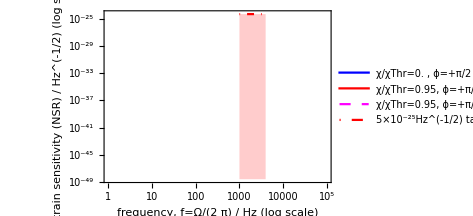
-Graphics-
-Graphics-
-Graphics-

```mathematica
(*setting configuration and derived parameters*)
setConfigParamsLi2020[2π 1. 10^3]
printParams[]

χRatio0=0.95;
pumpPhase0=π/2;
valsList1={
{0,pumpPhase0,Tla0,Tlb0,Tlc0,Rpd0,True,False,True},
{χRatio0 singularityThr[Tla0,Tlb0,Tlc0,True](*calculated for symSRM=True*),pumpPhase0,Tla0,Tlb0,Tlc0,Rpd0,True,False,True},
{χRatio0 singularityThr[Tla0,Tlb0,Tlc0,False](*calculated for symSRM=True*),pumpPhase0,Tla0,Tlb0,Tlc0,Rpd0,True,False,False}};
plotwRP[valsList1,None,{Blue,Red,{Magenta,Dashed}},{1,10^5}]
```

```mathematica
valsList1={
{0,pumpPhase0,0,0,0,0,False,False,False},
{0.995ωs,pumpPhase0,0,0,0,0,False,False,False},
{ωs,pumpPhase0,0,0,0,0,False,False,False}};
plotwRP[valsList1,None,{Orange,Green,Red},{1,10^5}]
```

```mathematica
valsList1={
{0,pumpPhase0,Tla0,Tlb0,Tlc0,Rpd0,True,False,False},
{χRatio0 singularityThr[Tla0,Tlb0,Tlc0,False],pumpPhase0,Tla0,Tlb0,Tlc0,Rpd0,True,False,False}};
plotwRP[valsList1,None,{Blue,Red},{1,10^5}]
```

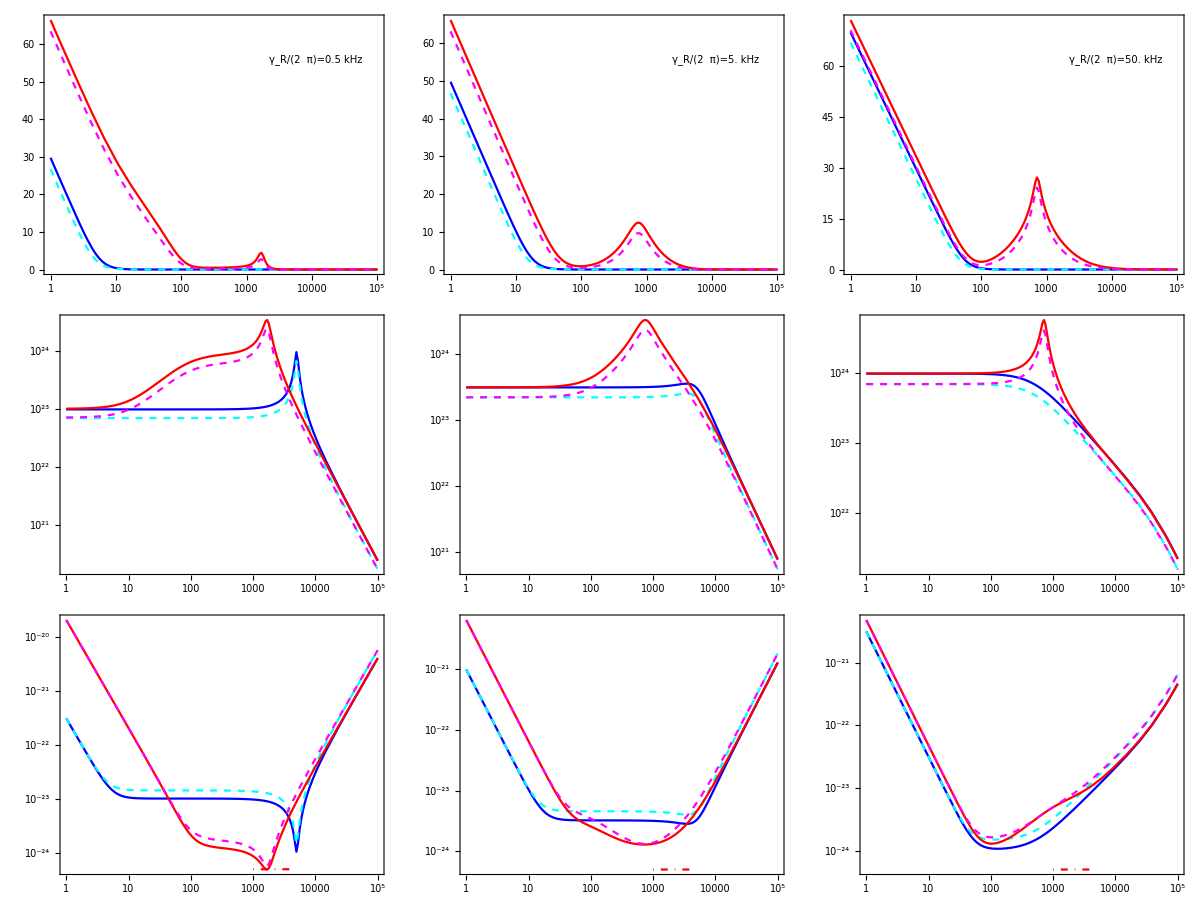
-Graphics-nondegenerate internal squeezing
parameters of Li et al, 2020; changing γ_R | signal | quantum noise
sensitivity (NSR) | transfer function | transfer function
/ Hz^(-1/2) (log scale) | / [?] (log scale) | / dB (20 log_10)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
(*showing nIS tolerance to detection losses, vary Rpd from 0 to 0.95, 0.0005 is the quantum efficiency of the PD in aLIGO
--> point is that with 10% loss in the output chain, nIS is not affected very much
NB: if the same is done for squeezer off, then results look the same, so it doesn't look like nIS is even more resilient than before? at the very least, it isn't definitive by eye*)
valsListHeld={
{0,pumpPhase0,Tla0,Tlb0,Tlc0,0,True,False,False},
{0,pumpPhase0,Tla0,Tlb0,Tlc0,0.5,True,False,False},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0,False]],pumpPhase0,Tla0,Tlb0,Tlc0,0,True,False,False},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0,False]],pumpPhase0,Tla0,Tlb0,Tlc0,0.5,True,False,False}};
plotγRGrid[
{2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020; changing γ_R",None(*see γRList*),2π 5000},
{2π 0.5 10^3,2π 5. 10^3,2π 50. 10^3},
valsListHeld,{Blue,{Cyan,Dashed},Red,{Magenta,Dashed}},{1,10^5}]
(*Export["nIS_sigRO_tolerance_Rpd.pdf",%];*)
```

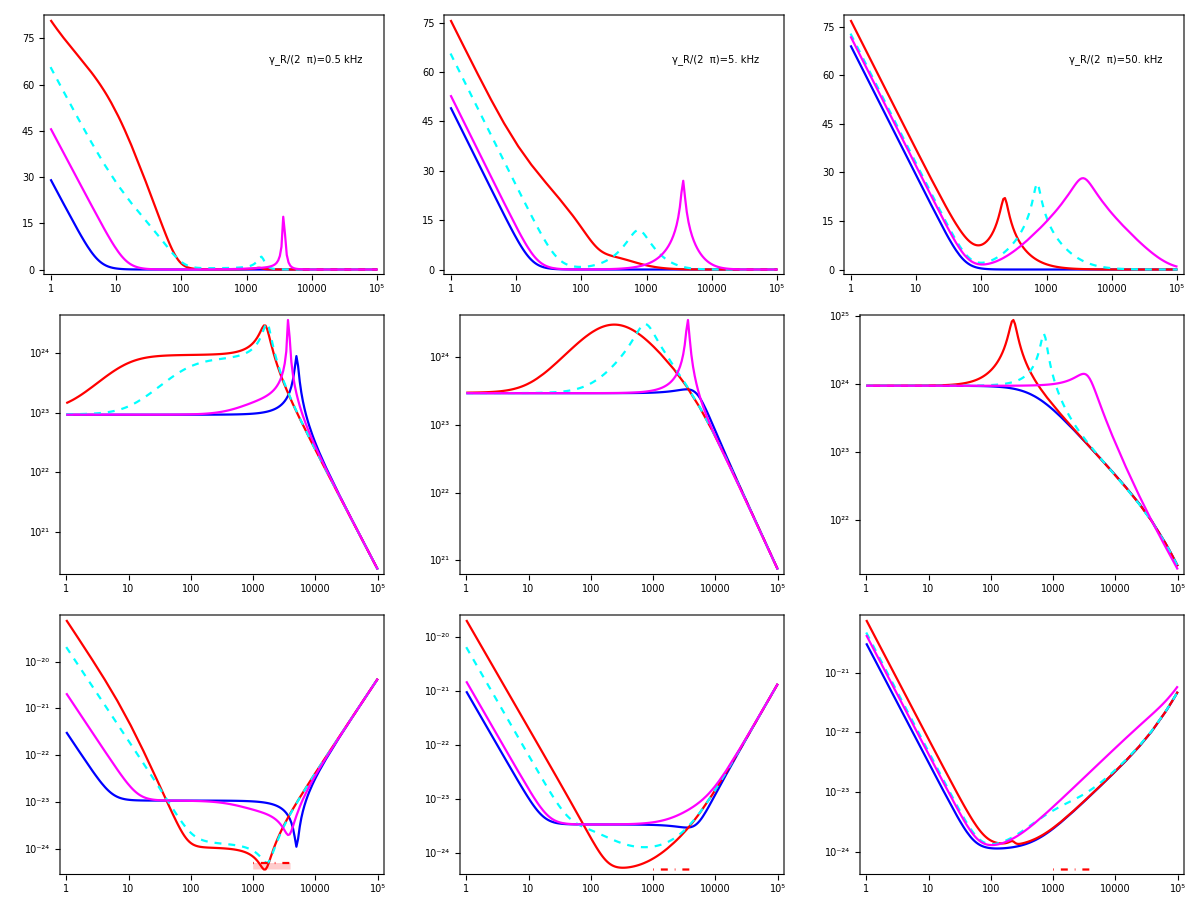
-Graphics-nondegenerate internal squeezing
parameters of Li et al, 2020 but changing γ_R | signal | quantum noise
sensitivity (NSR) | transfer function | transfer function
/ Hz^(-1/2) (log scale) | / [?] (log scale) | / dB (20 log_10)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
(*showing nIS tolerance to idler losses, vary Tlc from 0 to 1000ppm=0.001 to 100000ppm=0.1,
in order to have the singularity threshold not swap over to the DC pole, need γa≤γc, so don't use γc=0 unless γa=0 as well
swapping over is not unphysical, but it is a good test of the regieme of "large arm loss"*)
Tla1=0.5Tla0;
idlerLossList={100.,1000.,1000.} 10^-6;
valsListHeld={
{0,pumpPhase0,Tla1,Tlb0,idlerLossList[[1]],Rpd0,True,False,False},
{χRatio0 Hold[singularityThr[Tla1,Tlb0,idlerLossList[[1]],False]],pumpPhase0,Tla1,Tlb0,idlerLossList[[1]],Rpd0,True,False,False},
{χRatio0 Hold[singularityThr[Tla1,Tlb0,idlerLossList[[2]],False]],pumpPhase0,Tla1,Tlb0,idlerLossList[[2]],Rpd0,True,False,False},
{χRatio0 Hold[singularityThr[Tla1,Tlb0,idlerLossList[[3]],True]],pumpPhase0,Tla1,Tlb0,idlerLossList[[3]],Rpd0,True,False,True}};
plotγRGrid[
{2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020 but changing γ_R",None(*see γRList*),2π 5000},
{2π 0.5 10^3,2π 5. 10^3,2π 50. 10^3},
valsListHeld,{Blue,Red,{Cyan,Dashed},Magenta},{1,10^5}]
```

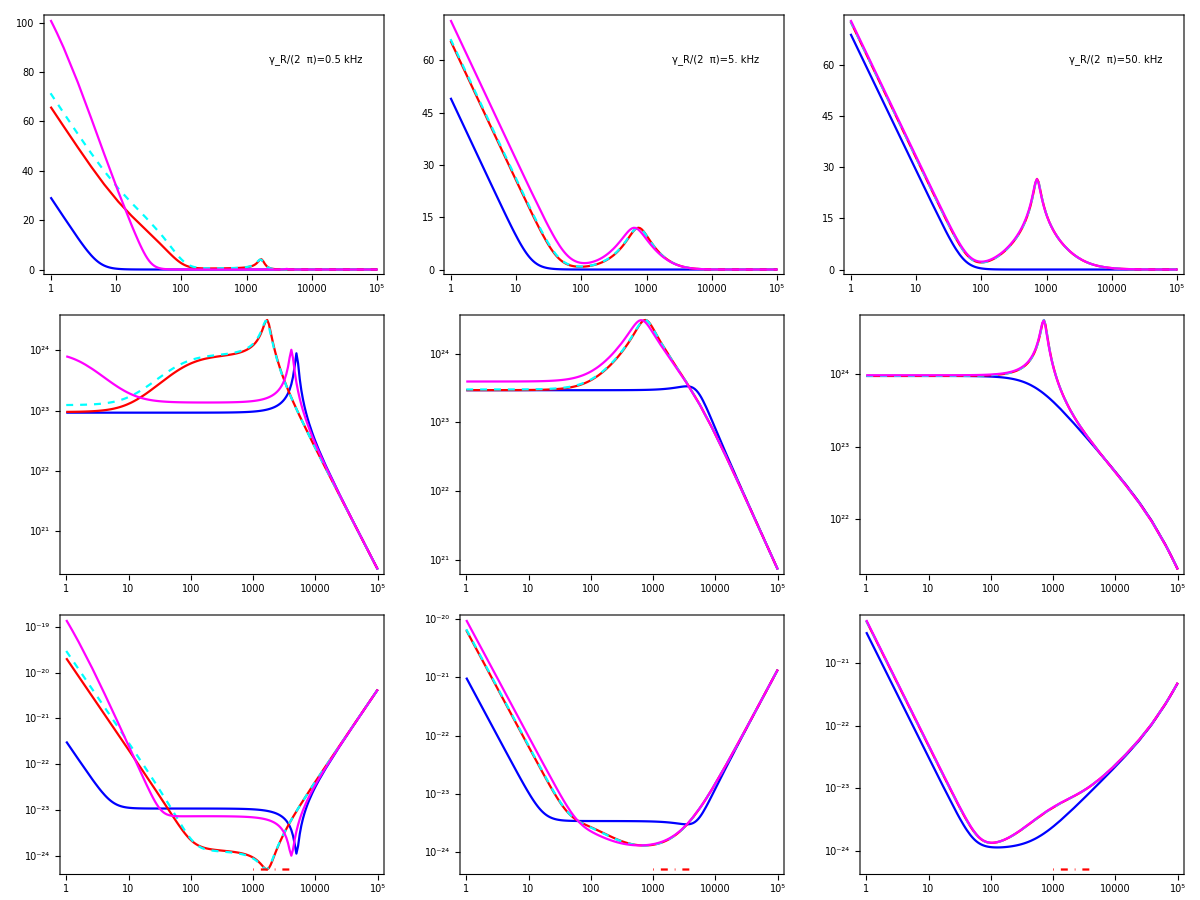
-Graphics-nondegenerate internal squeezing
parameters of Li et al, 2020; changing γ_R | signal | quantum noise
sensitivity (NSR) | transfer function | transfer function
/ Hz^(-1/2) (log scale) | / [?] (log scale) | / dB (20 log_10)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
(*for completeness, tolerance to arm loss and signal loss
--> arm loss has the added point that singularity threshold changes around γa=γc, also appears to matter less as γR increases
--> signal loss appears to have little effect, compare Tlb to Tsrm*)
valsListHeld={
{0,pumpPhase0,Tla0,Tlb0,Tlc0,Rpd0,True,False,False},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0,False]],pumpPhase0,Tla0,Tlb0,Tlc0,Rpd0,True,False,False},
{χRatio0 Hold[singularityThr[10Tla0,Tlb0,Tlc0,False]],pumpPhase0,10Tla0,Tlb0,Tlc0,Rpd0,True,False,False},
{χRatio0 Hold[singularityThr[100Tla0,Tlb0,Tlc0,False]],pumpPhase0,100Tla0,Tlb0,Tlc0,Rpd0,True,False,False}};
plotγRGrid[
{2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020; changing γ_R",None(*see γRList*),2π 5000},
{2π 0.5 10^3,2π 5. 10^3,2π 50. 10^3},
valsListHeld,{Blue,Red,{Cyan,Dashed},Magenta},{1,10^5}]
Export["nIS_sigRO_tolerance_Tla.pdf",%];
```

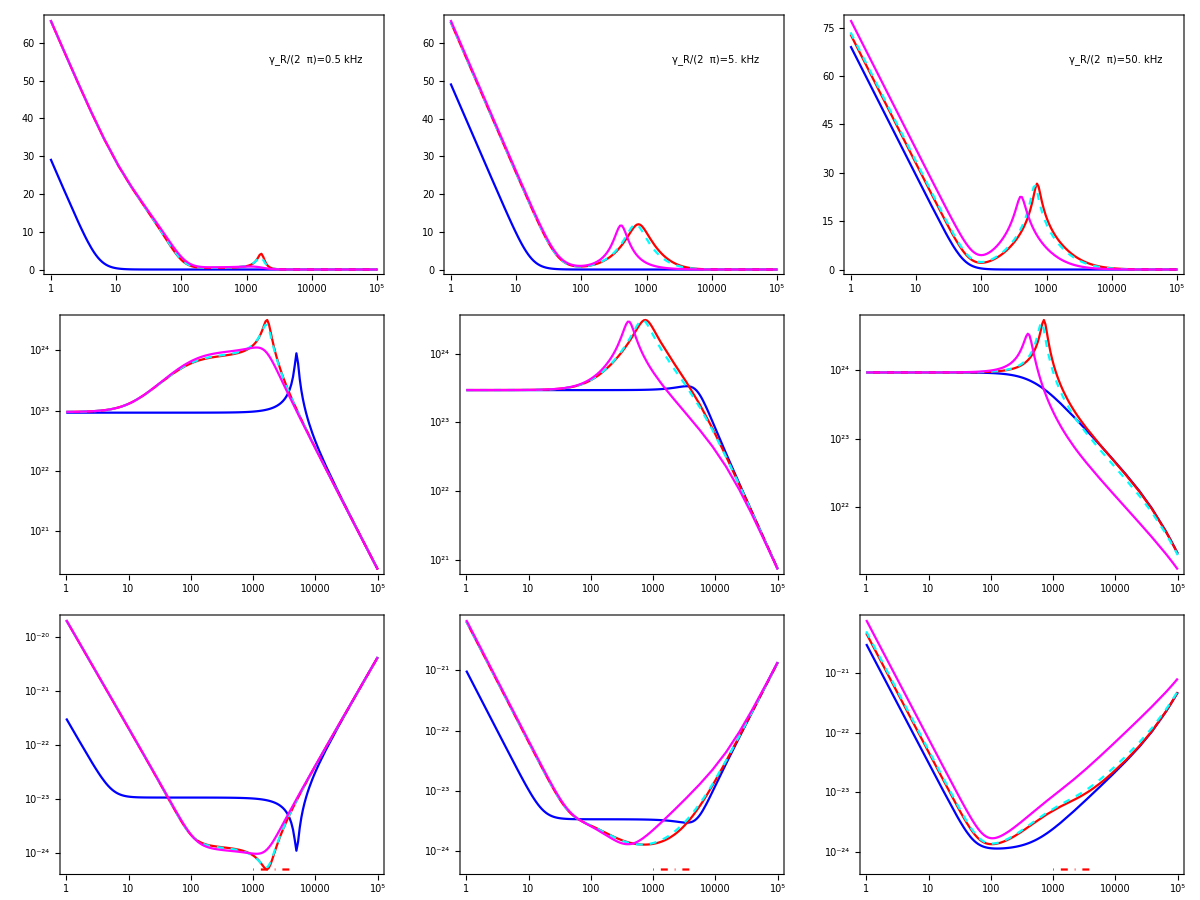
-Graphics-nondegenerate internal squeezing
parameters of Li et al, 2020; changing γ_R | signal | quantum noise
sensitivity (NSR) | transfer function | transfer function
/ Hz^(-1/2) (log scale) | / [?] (log scale) | / dB (20 log_10)frequency, f=Ω/(2  π) / Hz (log scale)

```mathematica
valsListHeld={
{0,pumpPhase0,Tla0,Tlb0,Tlc0,Rpd0,True,False,False},
{χRatio0 Hold[singularityThr[Tla0,Tlb0,Tlc0,False]],pumpPhase0,Tla0,Tlb0,Tlc0,Rpd0,True,False,False},
{χRatio0 Hold[singularityThr[Tla0,10Tlb0,Tlc0,False]],pumpPhase0,Tla0,10Tlb0,Tlc0,Rpd0,True,False,False},
{χRatio0 Hold[singularityThr[Tla0,100Tlb0,Tlc0,False]],pumpPhase0,Tla0,100Tlb0,Tlc0,Rpd0,True,False,False}};
plotγRGrid[
{2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020; changing γ_R",None(*see γRList*),2π 5000},
{2π 0.5 10^3,2π 5. 10^3,2π 50. 10^3},
valsListHeld,{Blue,Red,{Cyan,Dashed},Magenta},{1,10^5}]
Export["nIS_sigRO_tolerance_Tlb.pdf",%];
```

```mathematica
(*lossless nIS, to compare to Fig. 5 in Li et al, 2020*)
valsListHeld={
{0,pumpPhase0,0,0,0,0,True,False,False},
{χRatio0 Hold[singularityThr[0,0,0,False]](*calculated for symSRM=True*),pumpPhase0,0,0,0,0,True,False,False}};
plotγRGrid[
{2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020; changing γ_R",None(*see γRList*),2π 5000},
{2π 0.5 10^3,2π 5. 10^3,2π 50. 10^3},
valsListHeld,{Blue,{Magenta,Dashed}},{1,10^5}]
```

configuration parameters:
paramSetName=Li et al, 2020 + 400. kg, λ0=2.×10^-6 m, Larm=4. km, Lsrc=Lsrc m, Pcirc=3. MW, Titm=Titm, Tsrm=0.046, M=400. kg
derived parameters:
ωFSR/(2  π)=1/τRoundTripArm=37.5 kHz, 1/τRoundTripSRC=133. kHz, γR/(2  π)=0.5 kHz, ωs/(2  π)=5. kHz; ωs/γR=10.

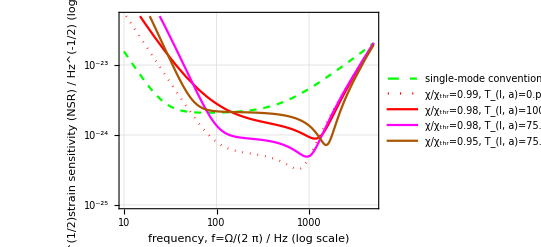

```mathematica
(*comparing nIS to sWLC*)
(*single-mode detector, i.e. no SRC*)
ASDShConwRP[Ω0_?NumericQ,Tla_?NumericQ,Rpd0_?NumericQ,ρRPTrue_:True]:=Re[Sqrt[(2 (γa+γR) ρRP^2)/(β^2 Ω^4 ((γa+γR)^2+Ω^2))+((γa+γR)^2+Ω^2)/(4 β^2 γR-4 Rpd β^2 γR)]]/.{
Ω->Ω0,γa->γaFn[Tla],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0]}

plotSMConwRP[valsList_,plotLabel_:None,plotStyle_:{},fRange_:{10,5000}]:=(
{fmin,fmax}=fRange;
LogLogPlot[Evaluate[Join[{2^(1/2)ASDShConwRP[2π f,0,0]},
Table[2^(1/2)ASDShwRP@@Join[{2π f},valsList[[i]]],{i,1,Length[valsList]}]]],
{f,fmin,fmax},ImageSize->400,PlotLegends->LineLegend[Join[{"single-mode conventional detector"},Table[legendStylerShort[valsList[[i]]],{i,1,Length[valsList]}]],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],PlotStyle->({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[valsList],Length[plotStyle]],{0,Length[valsList]}];
Join[{Directive[Green,Dashed]},Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}]]),PlotRange->{{fmin,fmax},{10^-25,5 10^-23}},Frame->True,FrameLabel->{{"2^(1/2)strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)",},{"frequency, f=Ω/(2  π) / Hz (log scale)","nondegenerate internal squeezing\nparameters of "<>paramSetName<>" and a factor of two in S_h (from T norm.?)\ncompare to Fig.5 from Li et al, 2020"}},
PerformanceGoal->"Speed",GridLines->Automatic])

(*plotting with the extra factor of 2 just to compare --> result good at HF and peak, but disagrees at LF?*)
setConfigParamsCustom[2./10^6,4. 10^3,None,3. 10^6,None,0.046,400.,"Li et al, 2020 + 400. kg",2 π 500.,2 π 5000.]
printParams[]
(*LogLogPlot[{2^(1/2)ASDShConwRP[2π f,0,0]},{f,10,5000},PlotRange->{10^-25,5 10^-23},GridLines->Automatic,PlotStyle->{Directive[Green,Dashed]},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)",},{"frequency, f=Ω/(2 π) / Hz (log scale)","single-mode conventional detector\nparameters of "<>paramSetName<>"\nwith factor of two, normalisation issue?"}}]*)

(*using 98% χThr like Li*)
Tla1=75. 10^-6;Tlb1=Tlb0;Tlc1=100. 10^-6;
valsList1={{2π 4.93 10^3(*Hz*),π/2,0,0,0,0,True,False,False},{0.98singularityThr[Tla0,Tlb0,Tlc0,False],π/2,Tla0,Tlb0,Tlc0,Rpd0,True,False,False},{0.98singularityThr[Tla1,Tlb1,Tlc1,False],π/2,Tla1,Tlb1,Tlc1,Rpd0,True,False,False},{0.95singularityThr[Tla1,Tlb1,Tlc1,False],π/2,Tla1,Tlb1,Tlc1,Rpd0,True,False,False}};
plotSMConwRP[valsList1,,{{Red,Dotted},Red,Magenta,Darker[Orange]}]
(*needs to use SQL formula with added factor of 2^(1/2), i.e. 2^(1/2)((4ℏ)/(M (2π f)^2 Larm^2))^(1/2), have cut SQL, but it is a bad sign for derivation*)
(*Fig. 5 from Li et al 2020: -Graphics--Graphics-*)
(*worsened by 2^(1/2) still achieves target at 1kHz*)
```

0.99016  0.999194

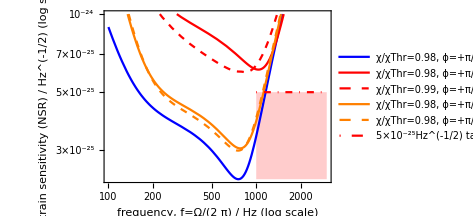

```mathematica
Print[singularityThr[Tla0,Tlb0,Tlc0,False]/singularityThr[0,0,0,False],"  ",singularityThr[Tla1,Tlb1,Tlc1,False]/singularityThr[0,0,0,False]]
valsList1={
{2π 4.93 10^3(*Hz, value from Li*),π/2,0,0,0,0,True,False,False},
{4.93/5(*using 98.6% χThr like Li*)singularityThr[Tla0,Tlb0,Tlc0,False],π/2,Tla0,Tlb0,Tlc0,Rpd0,True,False,False},
{4.93/5(*using 98.6% χThr like Li*)singularityThr[0,0,0,False],π/2,Tla0,Tlb0,Tlc0,Rpd0,True,False,False},
{4.93/5(*using 98.6% χThr like Li*)singularityThr[Tla1,Tlb1,Tlc1,False],π/2,Tla1,Tlb1,Tlc1,Rpd0,True,False,False},
{4.93/5(*using 98.6% χThr like Li*)singularityThr[0,0,0,False],π/2,Tla1,Tlb1,Tlc1,Rpd0,True,False,False}};
plotASDShwRP[valsList1,None,{Blue,Red,{Red,Dashed},Orange,{Orange,Dashed}},{100,3 10^3},None,{All,10^-24}]
(*therefore, the effect is small and can be left to future work*)
```

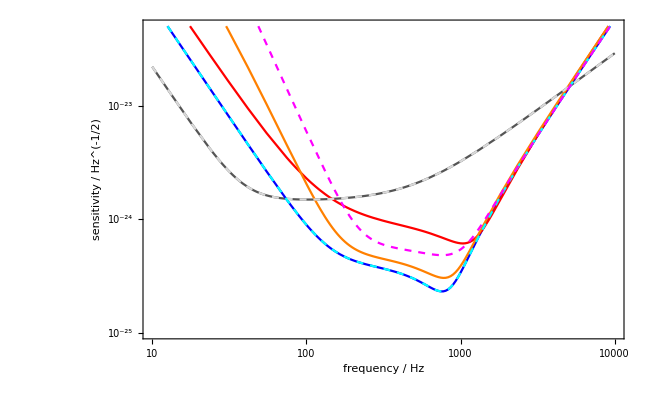

```mathematica
(*Li does not update their parameter (G) to lossy threshold*)
ASDShConwRP[Ω0_?NumericQ,Tla_?NumericQ,Rpd0_?NumericQ,ρRPTrue_:True]:=Re[Sqrt[(2 (γa+γR) ρRP^2)/(β^2 Ω^4 ((γa+γR)^2+Ω^2))+((γa+γR)^2+Ω^2)/(4 β^2 γR-4 Rpd β^2 γR)]]/.{
Ω->Ω0,γa->γaFn[Tla],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0]}
Tla1=75 10^-6;Tlb1=Tlb0;Tlc1=100. 10^-6;
setConfigParamsCustom[2./10^6,4. 10^3,None,3. 10^6,None,0.046,200.,"Li et al, 2020 + 400. kg",2 π 500.,2 π 5000.]
valsList1={
{2π 4.93 10^3(*Hz, value from Li*),π/2,0,0,0,0,True,False,False},
{4.93/5(*using 98.6% χThr like Li*)singularityThr[Tla0,Tlb0,Tlc0,False],π/2,Tla0,Tlb0,Tlc0,Rpd0,True,False,False},
{4.93/5(*using 98.6% χThr like Li*)singularityThr[Tla1,Tlb1,Tlc1,False],π/2,Tla1,Tlb1,Tlc1,Rpd0,True,False,False}};
plotStyle0={Darker[Gray],Blue,Red,Orange,{LightGray,Dashed},{Cyan,Dashed},{Magenta,Dashed}};
monoS[str_]:=Style[str,FontFamily->"Monospace"]
Labeled[LogLogPlot[Evaluate[Join[{ASDShConwRP[2π f,0,0]},Table[ASDShwRP@@Join[{2π f},valsList1[[i]]],{i,1,Length[valsList1]}],{
qnoisesc,qnoisewlc,totalnoisewlc}]],{f,10,10^4},Frame->True,FrameTicksStyle->Directive[14],FrameLabel->{{Style["sensitivity / Hz^(-1/2)",14],},{Style["frequency / Hz",14],}},ImageSize->650,PlotStyle->plotStyle0,PlotRange->{ 10^-25,5 10^-23},PerformanceGoal->"Speed"],Framed[
Block[{legendOrder={1->6,5->7,2->1,6->2,3->3,7->5,4->4}},
LineLegend[Permute[plotStyle0,SparseArray[legendOrder]],
Permute[Join[{"lossless, single-mode detector"},{"nondegenerate internal squeezing: lossless",
"nondegenerate internal squeezing: realistic optical losses",
"nondegenerate internal squeezing: optimistic optical losses"},{"Li et al, 2020: lossless, single-mode detector","Li et al, 2020: no optical loss, quantum noise–limited sensitivity","Li et al, 2020: no optical loss, quantum and thermal noise–limited sensitivity"}],SparseArray[legendOrder]],LabelStyle->Directive[14],LegendMarkerSize->{{25,15}}]],FrameStyle->Thin],Bottom]
Export["nIS_vs_sWLC.pdf",%];
```

```mathematica
(*ballpark losses required to hit 5e-25 sensitivity target from Miao et al 2018, noting that the sWLC overlay aove has an extra factor of two improvement in sensitivity*)
Tla1=75. 10^-6;Tlb1=Tlb0;Tlc1=100. 10^-6;Rpd1=Rpd0;
χRatio1=0.98;
valsListHeld={
{0,pumpPhase0,Tla1,Tlb1,Tlc1,Rpd1,True,False,False},
{χRatio1 Hold[singularityThr[Tla1,Tlb1,Tlc1,False]],pumpPhase0,Tla1,Tlb1,Tlc1,Rpd1,True,False,False}};
plotγRGrid[
{2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),"Li et al, 2020 + changing γ_R + ωs increased",None(*see γRList*),2π 10000},
{2π 0.5 10^3,2π 5. 10^3,2π 50. 10^3},
valsListHeld,{Blue,Red},{1,10^5}]
```

```mathematica
setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,200(*kg*),None,2π 500,2π 5000]
valsList1={
{0,pumpPhase0,Tla1,Tlb1,Tlc1,Rpd1,True,False,False},
{0.95 singularityThr[Tla1,Tlb1,Tlc1,False],pumpPhase0,Tla1,Tlb1,Tlc1,Rpd1,True,False,False}};
plotwRP[valsList1,None,{Blue,Red},{100,5 10^4}]
```

```mathematica
(*NB: radiation pressure worsened because squeezing is in phase quadrature,
to-do: frequency dependent internal squeezing?
--> we now have pump parameter -- so use /.ϕ->ϕFn[...]?*)
```

```mathematica
(*to-do: copy other plotting functions from sWLC:,
- stability --> not necessary, same denominator in transfer functions so same stability,
- noise "budget" (transfer functions) --> done, but I don't know how to turn off shot noise? ,
- optimum sensitivity at probe frequency --> done, 2.5k is most interesting,
*)
```

```mathematica
(*noise "budget",
to-do: turn shot noise off to plot radiation pressure separately, how?*)
RpdwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:False,symSRM_:True]:=Re[Sqrt[(Rpd Id)[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
RinwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:False,symSRM_:True]:=Re[Sqrt[(Rin.ConjugateTranspose[Rin])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
RawRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:False,symSRM_:True]:=Re[Sqrt[(Ra.ConjugateTranspose[Ra])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
RbwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:False,symSRM_:True]:=Re[Sqrt[(Rb.ConjugateTranspose[Rb])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
RcwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:False,symSRM_:True]:=Re[Sqrt[(Rc.ConjugateTranspose[Rc])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}

plotNoiseBudgetwRP[params_,fRange_:{10,10^4}]:=
LogLinearPlot[Evaluate[{
20Log10[1],
20Log10[RinwRP@@Join[{2π f},params]],
20Log10[RawRP@@Join[{2π f},params]],
20Log10[RbwRP@@Join[{2π f},params]],
20Log10[RcwRP@@Join[{2π f},params]],
20Log10[RpdwRP@@Join[{2π f},params]],
20Log10[QNwRP@@Join[{2π f},params]]}],{f,fRange[[1]],fRange[[2]]},PlotLegends->LineLegend[{"vacuum","R_in, behind SRM","(R^(L))_a, arm intra-cav.","(R^(L))_b, SRC signal intra-cav.","(R^(L))_c, SRC idler intra-cav.","(R^(L))_PD, PD loss","total quantum noise"},LabelStyle->Directive[10],LegendLabel->legendStyler[params]],PlotRange->All,PlotStyle->{Directive[Gray,Dashed],,,,,,Directive[Black,Dashed]},Frame->True,FrameLabel->{{"quantum noise transfer function,\n|R| / dB (20log10)",},{"frequency, f=Ω/(2  π) / Hz","nondegenerate internal squeezing\nparameters of "<>paramSetName}},PerformanceGoal->"Speed"]
Clear[plotNoiseBudgetwRPPretty]
plotNoiseBudgetwRPPretty[params_,plotStyle_,fRange_:{10,10^4}]:=
LogLinearPlot[Evaluate[{
20Log10[RinwRP@@Join[{2π f},params]],
20Log10[RawRP@@Join[{2π f},params]],
20Log10[RbwRP@@Join[{2π f},params]],
20Log10[RcwRP@@Join[{2π f},params]],
20Log10[RpdwRP@@Join[{2π f},params]],
20Log10[QNwRP@@Join[{2π f},params]]}],{f,fRange[[1]],fRange[[2]]},PlotLegends->LineLegend[{"readout port vacuum","arm intra-cavity loss","signal intra-cavity loss","idler intra-cavity loss","detection loss","total quantum noise"},LabelStyle->Directive[14],LegendLabel->legendStylerSplit[params]],PlotRange->All,PlotStyle->Join[plotStyle,{Directive[Black,Dashed]}],Frame->True,FrameLabel->{{Style["noise response\n/ dB (20log_10)",14],},{Style["frequency, f=Ω/(2  π) / Hz (log scale)",14],}},FrameTicksStyle->Directive[FontSize->14],PerformanceGoal->"Speed" (*Quality looks the same*)]
```

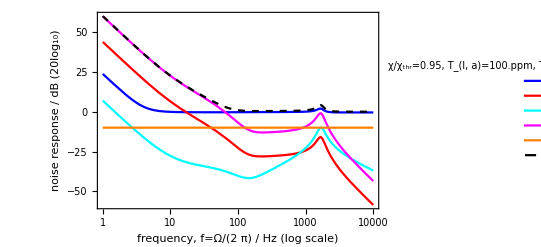

```mathematica
setConfigParamsLi2020[]
χRatio0=0.95;
(*plotNoiseBudgetwRP[{χRatio0 ωs,π/2,Tla0,Tlb0,Tlc0,Rpd0,True,False,True}]*)
plotNoiseBudgetwRPPretty[{χRatio0 singularityThr[Tla0,Tlb0,Tlc0,False],π/2,Tla0,Tlb0,Tlc0,Rpd0,True,False,False},{Blue,Red,Cyan,Magenta,Orange},{1,10 10^3}]
Export["nIS_sigRO_noise_budget.pdf",%];
(*pumpPhase0=3/4 π;
plotNoiseBudgetwRP[{χRatio0 ωs,pumpPhase0,0.1,0.1,0.1,0.1,False}]
plotNoiseBudgetwRP[{χRatio0 ωs,pumpPhase0,0.1,0.1,0.1,0.1,True,True}]*)
(*BAE 2nd peak (if real, not a bug) appears in all noise transfer functions (except Rpd ofc)*)
```

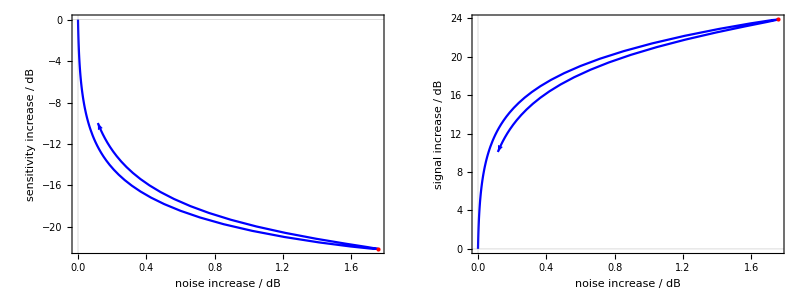

```mathematica
(*optimum sensitivity at probe frequency*)
(*see old commit before October 7th for original plot*)
(*pastThr requires maxThrRatio=1*)
Clear[plotThresholdFinder]
plotThresholdFinder[fProbe_,Tla_,Tlb_,Tlc_,ϕ_:π/2,pastThreshold_:False,ρRPTrue_:True,ρBAETrue_:False,symSRM_:False]:=(
(*reference now has loss*)
probeNoiseRef=QNwRP[2π fProbe,0,ϕ,Tla,Tlb,Tlc,Rpd0,ρRPTrue,ρBAETrue,False];
probeSigRef=sigwRP[2π fProbe,0,ϕ,Tla,Tlb,Tlc,Rpd0,ρRPTrue,ρBAETrue,False];
probeSensRef=ASDShwRP[2π fProbe,0,ϕ,Tla,Tlb,Tlc,Rpd0,ρRPTrue,ρBAETrue,False];
maxThrRatio=1;
pointRatio=0.875;
rpdList={Rpd0};
leftPadding=60;
imageSize=250;
arrowHeads={{0.04,0.6},{0.04,0.9}};
p1=ParametricPlot[Evaluate[Flatten[Table[{
{20Log10[QNwRP[2π fProbe,χRatio singularityThr[Tla,Tlb,Tlc,symSRM],ϕ,Tla,Tlb,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],20Log10[ASDShwRP[2π fProbe,χRatio singularityThr[Tla,Tlb,Tlc,symSRM],ϕ,Tla,Tlb,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeSensRef]}},{i,1,Length[rpdList]}],1]],{χRatio,0,maxThrRatio},Frame->True,FrameTicksStyle->Directive[FontSize->14],FrameLabel->{{Style[StringForm["sensitivity increase / dB",N[fProbe/10^3]],16],},{Style[StringForm["noise increase / dB",N[fProbe/10^3]],16,FontFamily->"Arial"],}},PlotStyle->{Blue}(*Table[Blend[{Blue,Green},(i-1)/(Length[rpdList]-1)],{i,1,Length[rpdList]}]*),PlotRange->All,ImagePadding->{{60,10},{50,1}},ImageSize->{Automatic,imageSize},AspectRatio->3/4,PerformanceGoal->"Speed",GridLines->{{0},{0}},Epilog->{Red,PointSize[Large],Point[{{20Log10[QNwRP[2π fProbe,pointRatio singularityThr[Tla,Tlb,Tlc,symSRM],ϕ,Tla,Tlb,Tlc,Rpd0,ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],20Log10[ASDShwRP[2π fProbe,pointRatio singularityThr[Tla,Tlb,Tlc,symSRM],ϕ,Tla,Tlb,Tlc,Rpd0,ρRPTrue,ρBAETrue,symSRM]/probeSensRef]}}]}]/.Line[x__]:>Sequence[Arrowheads->arrowHeads,Arrow[x]];
(*p2=ParametricPlot[Evaluate[{
{20Log10[QNwRP[2π fProbe,maxThrRatio singularityThr[Tla,Tlb,Tlc,symSRM],ϕ,Tla,Tlb,Tlc,Rpd,ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],20Log10[ASDShwRP[2π fProbe,maxThrRatio singularityThr[Tla,Tlb,Tlc,symSRM],ϕ,Tla,Tlb,Tlc,Rpd,ρRPTrue,ρBAETrue,symSRM]/probeSensRef]}}],{Rpd,rpdList[[1]],rpdList[[-1]]},Frame->True,PlotStyle->Directive[Black],PlotLegends->LineLegend[{Style[StringForm["χ/χ_thr=``, varying R_PD∈(``,``)",NumberForm[maxThrRatio],NumberForm[N[rpdList[[1]]]],NumberForm[N[rpdList[[-1]]]]],14]},LabelStyle->Directive[10]],PlotRange->All,ImagePadding->{{leftPadding,10},{1,All}},ImageSize->350,PerformanceGoal->"Speed"];*)
If[pastThreshold,
p1b=ParametricPlot[Evaluate[Flatten[Table[{
{20Log10[QNwRP[2π fProbe,χRatio singularityThr[Tla,Tlb,Tlc,symSRM],ϕ,Tla,Tlb,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],20Log10[ASDShwRP[2π fProbe,χRatio singularityThr[Tla,Tlb,Tlc,symSRM],ϕ,Tla,Tlb,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeSensRef]}},{i,1,Length[rpdList]}],1]],{χRatio,maxThrRatio,2},Frame->True,PlotStyle->Table[Blend[{Red,Yellow},(i-1)/(Length[rpdList]-1)],{i,1,Length[rpdList]}],PlotLegends->LineLegend[{Table[StringForm["χ/χ_thr∈(``,2), R_PD=``",maxThrRatio,NumberForm[N[rpdList[[i]]]]],{i,1,Length[rpdList]}]},LabelStyle->Directive[10]],PlotRange->All,ImagePadding->{{leftPadding,10},{1,All}},ImageSize->imageSize,PerformanceGoal->"Speed"];
p1and2=Show[p1,p1b(*,p2*)];,
p1and2=Show[p1(*,p2*)];];
p3=ParametricPlot[Evaluate[Flatten[Table[{
{20Log10[QNwRP[2π fProbe,χRatio singularityThr[Tla,Tlb,Tlc,symSRM],ϕ,Tla,Tlb,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],20Log10[sigwRP[2π fProbe,χRatio singularityThr[Tla,Tlb,Tlc,symSRM],ϕ,Tla,Tlb,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeSigRef]}},{i,1,Length[rpdList]}],1]],{χRatio,0,maxThrRatio},Frame->True,FrameTicksStyle->Directive[FontSize->14],FrameLabel->{{Style[StringForm["signal increase / dB",N[fProbe/10^3]],16],},{Style[StringForm["noise increase / dB",N[fProbe/10^3]],16,FontFamily->"Arial"],}},PlotStyle->{Blue},PlotRange->{All,{All,24.9}},ImagePadding->{{45,10},{50,1}},ImageSize->{Automatic,imageSize},AspectRatio->3/4,PerformanceGoal->"Speed",GridLines->{{0},{0}},Epilog->{Red,PointSize[Large],Point[{{20Log10[QNwRP[2π fProbe,pointRatio singularityThr[Tla,Tlb,Tlc,symSRM],ϕ,Tla,Tlb,Tlc,Rpd0,ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],20Log10[sigwRP[2π fProbe,pointRatio singularityThr[Tla,Tlb,Tlc,symSRM],ϕ,Tla,Tlb,Tlc,Rpd0,ρRPTrue,ρBAETrue,symSRM]/probeSigRef]}}]}]/.Line[x__]:>Sequence[Arrowheads->arrowHeads,Arrow[x]];
(*p4=ParametricPlot[Evaluate[
{20Log10[QNwRP[2π fProbe,maxThrRatio singularityThr[Tla,Tlb,Tlc,symSRM],ϕ,Tla,Tlb,Tlc,Rpd,ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],
20Log10[sigwRP[2π fProbe,maxThrRatio singularityThr[Tla,Tlb,Tlc,symSRM],ϕ,Tla,Tlb,Tlc,Rpd,ρRPTrue,ρBAETrue,symSRM]/probeSigRef]}],{Rpd,rpdList[[1]],rpdList[[-1]]},Frame->True,PlotStyle->Directive[Black],PlotRange->All,ImagePadding->{{leftPadding,10},{All,1}}];*)
If[pastThreshold,
p3b=ParametricPlot[Evaluate[Flatten[Table[{
{20Log10[QNwRP[2π fProbe,χRatio singularityThr[Tla,Tlb,Tlc,symSRM],ϕ,Tla,Tlb,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],20Log10[sigwRP[2π fProbe,χRatio singularityThr[Tla,Tlb,Tlc,symSRM],ϕ,Tla,Tlb,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeSigRef]}},{i,1,Length[rpdList]}],1]],{χRatio,maxThrRatio,2},Frame->True,PlotStyle->Table[Blend[{Red,Yellow},(i-1)/(Length[rpdList]-1)],{i,1,Length[rpdList]}],PlotRange->All,ImagePadding->{{leftPadding,10},{1,All}},ImageSize->imageSize,PerformanceGoal->"Speed"];
p3and4=Show[p3,p3b(*,p4*)];,
p3and4=Show[p3(*,p4*)];];
Grid[{{p1and2,p3and4}},Spacings->0])
(*LineLegend[{Blue},Table[Style[StringForm["χ/χ_thr∈(0,``), R_PD=``",NumberForm[maxThrRatio],NumberForm[N[rpdList[[i]]]]],14],{i,1,Length[rpdList]}],LabelStyle->Directive[10],LegendLabel->Style[StringForm["T_(l, a)=``ppm,\nT_(l, b)=``ppm,\nT_(l, c)=``ppm``"<>If[Not[ρRPTrue],"; no RP",""]<>If[ρBAETrue,"; with BAE",""],NumberForm[N[Tla 10^6]],NumberForm[N[Tlb 10^6]],NumberForm[N[Tlc 10^6]],If[ϕ≠π/2,",\nϕ/(2π)="<>ToString[NumberForm[N[ϕ/(2π)]]],""]],14]]*)

(*fProbe_,Tlc_,ϕ_:π/2,pastThreshold_:False,ρRPTrue_:True,ρBAETrue_:False,symSRM_:False*)
setConfigParamsLi2020[]
plotThresholdFinder[2500(*Hz*),Tla0,Tlb0,Tlc0,π/2,False]
Export["nIS_optimum_squeezing.pdf",%];
(*plotThresholdFinder[10(*Hz*),0.1,pumpPhase0]*)
(*
plotThresholdFinder[2500(*Hz*),0.1,pumpPhase0,False,True,True]
plotThresholdFinder[10(*Hz*),0.1,pumpPhase0,False,True,True]
*)
(*pump phase really affects low probe frequencies, but leaves kilohertz sensitivity relatively unchanged*)
```

lossless: {{Ω→1/2 ⅈ (-γR0+√(γR0^2-4 κ0^2+4 χ0^2))},{Ω→-1/2 ⅈ (γR0+√(γR0^2-4 κ0^2+4 χ0^2))}}

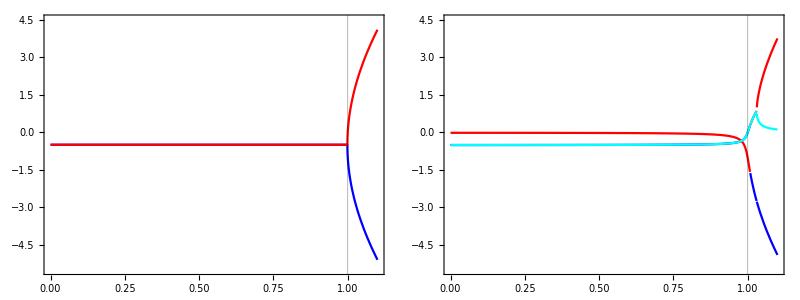
-Graphics-imaginary part of pole / γ_(b, R)ratio to singularity threshold, χ/χ_thr

```mathematica
(*copied from nIS.nb*)
(*Checking stability*)
Clear[χ]
denominator00=γbtot0-I Ω+κ0^2/(γa0-I Ω)-χ0^2/(γc0-I Ω);(*additional poles at γa,γc*)
Print["lossless: ",Solve[(denominator00/.{γa0->0,γc0->0,γbtot0->γR0})==0,Ω]]
(*stabilitySol=Simplify[Solve[denominator==0,Ω],Assumptions->{κ0>0,χ0>0,γa0>0,γbtot0>0,γc0>0}];*)
denom00[Tla_,Tlb_,Tlc_,symSRM_:True]:=γbtotFn[Tlb]-I Ω+ωs^2/(γaFn[Tla]-I Ω)-χ^2/(γcFn[Tlc,symSRM]-I Ω);

stabilitysWLC[Tla_,Tlb_,Tlc_,symSRM_:True]:=(
stabSol=NSolve[denom00[Tla,Tlb,Tlc,symSRM]==0,Ω];
p1=Plot[Evaluate[Table[(Im[Ω/.stabSol[[i]]]/.{χ->ratio ωs})/γR,{i,1,Length[stabSol]}]],{ratio,0,2},PlotStyle->{,Dashed,DotDashed},
ImagePadding->{{50,2},{1,All}},ImageSize->300,Frame->True,FrameLabel->{{"Im[Ω]/γR",},{,StringForm["poles of transfer function\nunstable when Im[Ω]≥0\nT_(l, a)=``, T_(l, b)=``, T_(l, c)=``, sym. SRM loss?=``",Tla,Tlb,Tlc,symSRM]}},GridLines->{{{1,Red}},None}];
p2=Plot[Evaluate[Table[(Re[Ω/.stabSol[[i]]]/.{χ->ratio ωs})/γR,{i,1,Length[stabSol]}]],{ratio,0,2},PlotStyle->{,Dashed,DotDashed},
ImagePadding->{{50,2},{All,1}},ImageSize->300,Frame->True,FrameLabel->{{"Re[Ω]/γR",},{"χ/ωs",}},GridLines->{{{1,Red}},None}];
Column[{p1,p2}])

Clear[stabilitysWLCPretty]
stabilitysWLCPretty[Tla_,Tlb_,Tlc_,symSRM_:False,hideYAx_:False,plotStyle_:{},exclusions_:None]:=(
stabSol=NSolve[denom00[Tla,Tlb,Tlc,symSRM]==0,Ω];
(*Labeled[*)
Plot[Evaluate[Table[(Im[Ω/.stabSol[[i]]]/.{χ->ratio singularityThr[Tla,Tlb,Tlc,symSRM]})/γR,{i,1,Length[stabSol]}]],{ratio,0,1.1},
ImagePadding->{{If[hideYAx,2,20],10},{20,1}},ImageSize->{Automatic,220},Frame->True,FrameLabel->{{,},{,}},GridLines->{{{1,Directive[Black,Thin]}},None},FrameTicksStyle->{{If[hideYAx,Directive[FontOpacity->0,FontSize->0],Directive[FontSize->14]],},{Directive[FontSize->14],}},PlotRange->{{All,All},{-5.5,4.5}},PerformanceGoal->"Quality",PlotStyle->plotStyle,Exclusions->exclusions])(*,Style[StringForm["\n\nT_(l, a)=``ppm,\nT_(l, b)=``ppm,\nT_(l, c)=``ppm",NumberForm[N[Tla 10^6]],NumberForm[N[Tlb 10^6]],NumberForm[N[Tlc 10^6]]],14],{{Right,Top}}])*)
(*Tla_,Tlb_,Tlc_*)
setConfigParamsLi2020[]
Labeled[Grid[{{stabilitysWLCPretty[0,0,0,False,False,{Blue,Red},None],stabilitysWLCPretty[Tla0,Tlb0,Tlc0,False,True,{Blue,Red,Cyan},Automatic]}},Spacings->0],{Style["imaginary part of pole / γ_(b, R)",16,FontFamily->"Arial"],Style["ratio to singularity threshold, χ/χ_thr",16,FontFamily->"Arial"]},{Left,Bottom},RotateLabel->True]
Export["nIS_stability.pdf",%];
(*realistically, γc is at least γR, so the lossless plot is not useful*)
(*plots look much nicer with Li et al, 2020 parameter set*)
(*Exclusions -> None makes a strange line in the lossy case that I am going to assume is an error*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------*)
(*Optimisation and feasibility*)
```

```mathematica
(*broadband detection: optimising integrated sensitivity,
--> un-squeezed integral is bounded by finite circulating power through the Mizuno Limit,
to-do: bias kernel to encourage more broadband sens.?*)
Clear[plotOptimiseBroadband]
plotOptimiseBroadband[Tla_,Tlb_,Tlc_,Rpd_,symSRM_:True,fRange_:{0,∞},χRatioMax_:0.95]:=(
χthr=singularityThr[Tla,Tlb,Tlc,symSRM];
Print["χ sing. thr. (ratio to ωs) = ", NumberForm[χthr/ωs,4]];
optiFnInt[χRatio_?NumericQ]:=NIntegrate[(β ASDShwRP[2π f,χRatio χthr,π/2,Tla,Tlb,Tlc,Rpd,True,False,symSRM])^-2,{f,fRange[[1]],fRange[[2]]},MaxRecursion->10,PrecisionGoal->3,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}];
optiSolInt=FindMaximum[{optiFnInt[χRatio],0<χRatio<χRatioMax},χRatio];
Print["broadband optimisation: χ ratio to sing. thr. = ",NumberForm[χRatio/.optiSolInt[[2]],4],If[Abs[(χRatio/.optiSolInt[[2]])-χRatioMax]<10^-5(*tolerance*),", at max. ratio allowed",""]];
Print[plotASDShwRP[{
{0,π/2,Tla,Tlb,Tlc,Rpd,True,False,symSRM},
{(χRatio/.optiSolInt[[2]])χthr,π/2,Tla,Tlb,Tlc,Rpd,True,False,symSRM},
{χRatioMax χthr,π/2,Tla,Tlb,Tlc,Rpd,True,False,symSRM}
},None,{Directive[Thin,Black],,Directive[Dashed,Gray]}]])

(*peak sensitivity optimisation*)
plotOptimisePeak[Tla_,Tlb_,Tlc_,Rpd_,symSRM_:True,fRange_:{0,∞},χRatioMax_:0.95]:=(
χthr=singularityThr[Tla,Tlb,Tlc,symSRM];
Print["χ sing. thr. (ratio to ωs) = ", NumberForm[χthr/ωs,4]];
optiSol=NMaximize[{(β ASDShwRP[2π f,χRatio χthr,π/2,Tla,Tlb,Tlc,Rpd,True,False,symSRM])^-2,f>0,0<χRatio<χRatioMax},{f,χRatio}];
Print["peak sensitivity optimisation: χ ratio to sing. thr. = ",NumberForm[χRatio/.optiSol[[2]],4],If[Abs[(χRatio/.optiSol[[2]])-χRatioMax]<10^-5(*tolerance*),", at max. ratio allowed",""]];
Print[plotASDShwRP[{
{0,π/2,Tla,Tlb,Tlc,Rpd,True,False,symSRM},
{(χRatio/.optiSol[[2]])χthr,π/2,Tla,Tlb,Tlc,Rpd,True,False,symSRM},
{χRatioMax χthr,π/2,Tla,Tlb,Tlc,Rpd,True,False,symSRM}
},None,{Directive[Thin,Black],,Directive[Dashed,Gray]}]])

(*probe frequency sensitivity optimisation*)
plotOptimiseProbe[fProbe_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:True,fRange_:{0,∞},χRatioMax_:0.95]:=(
χthr=singularityThr[Tla,Tlb,Tlc,symSRM];
Print["χ sing. thr. (ratio to ωs) = ", NumberForm[χthr/ωs,4]];
optiSol=NMaximize[{(β ASDShwRP[2π fProbe,χRatio χthr,π/2,Tla,Tlb,Tlc,Rpd,True,False,symSRM])^-2,0<χRatio<χRatioMax},χRatio];
Print["probe frequency " ,NumberForm[fProbe,3]," Hz sensitivity optimisation: χ ratio to sing. thr. = ",NumberForm[χRatio/.optiSol[[2]],4],If[Abs[(χRatio/.optiSol[[2]])-χRatioMax]<10^-5(*tolerance*),", at max. ratio allowed",""]];
plotASDShwRP[{
{0,π/2,Tla,Tlb,Tlc,Rpd,True,False,symSRM},
{(χRatio/.optiSol[[2]])χthr,π/2,Tla,Tlb,Tlc,Rpd,True,False,symSRM},
{χRatioMax χthr,π/2,Tla,Tlb,Tlc,Rpd,True,False,symSRM}
},None,{Directive[Thin,Black],,Directive[Dashed,Gray]},{10,10^4},{{{fProbe,Red}},{}}])

(*broadband optimisation against kernel, i.e. mutriK*)
plotOptimiseμtricK1[Tla_,Tlb_,Tlc_,Rpd_,symSRM_:True,fRange_:{1 10^3,4 10^3},χRatioMax_:0.95]:=(
χthr=singularityThr[Tla,Tlb,Tlc,symSRM];
Print["χ sing. thr. (ratio to ωs) = ", NumberForm[χthr/ωs,4]];
ASDShCrit = 5 10^-25;(*from Miao et al, 2018*)
k1=1/9;
integrand[f_?NumericQ,χRatio_?NumericQ]:=Block[{Z=1/ASDShCrit^-2(ASDShwRP[2π f,χRatio χthr,π/2,Tla,Tlb,Tlc,Rpd,True,False,symSRM]^-2-ASDShCrit^-2)},If[Z<0,Z,Z Exp[-k1 Z]]];
optiFnInt[χRatio_?NumericQ]:=1/(fRange[[2]]-fRange[[1]])NIntegrate[integrand[f,χRatio],{f,fRange[[1]],fRange[[2]]},MaxRecursion->10,PrecisionGoal->3,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}];
optiSolInt=FindMaximum[{optiFnInt[χRatio],0<χRatio<χRatioMax},χRatio];
Print["μtricK1 optimisation: χ ratio to sing. thr. = ",NumberForm[χRatio/.optiSolInt[[2]],4],If[Abs[(χRatio/.optiSolInt[[2]])-χRatioMax]<10^-5(*tolerance*),", at max. ratio allowed",""]];
Print[plotASDShwRP[{
{0,π/2,Tla,Tlb,Tlc,Rpd,True,False,symSRM},
{(χRatio/.optiSolInt[[2]])χthr,π/2,Tla,Tlb,Tlc,Rpd,True,False,symSRM},
{χRatioMax χthr,π/2,Tla,Tlb,Tlc,Rpd,True,False,symSRM}
},None,{Directive[Thin,Black],,Directive[Dashed,Gray]},{10,10^5},{{#,Red}&/@fRange,{}}]])
```

χ sing. thr. (ratio to ωs) = 0.9902

probe frequency 2500 Hz sensitivity optimisation: χ ratio to sing. thr. = 0.8743

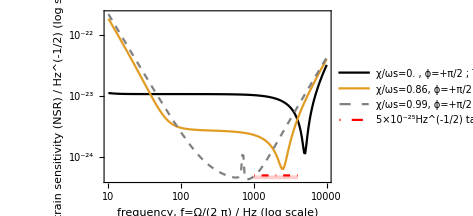

χ sing. thr. (ratio to ωs) = 0.9902

peak sensitivity optimisation: χ ratio to sing. thr. = 0.95, at max. ratio allowed

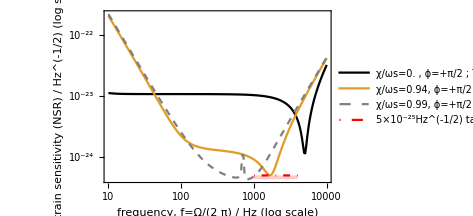

```mathematica
(*optimisation and plotting is slow, but faster for Li et al, 2020 parameter set?*)
plotOptimiseProbe[2500,Tla0,Tlb0,Tlc0,Rpd0,False]
plotOptimisePeak[Tla0,Tlb0,Tlc0,Rpd0,False]
```

```mathematica
printParams[]
```

configuration parameters:
paramSetName=Custom parameter set, λ0=2.×10^-6 m, Larm=4. km, Lsrc=Lsrc m, Pcirc=3 MW, Titm=Titm, Tsrm=0.046, M=200 kg
derived parameters:
ωFSR/(2  π)=1/τRoundTripArm=37.5 kHz, 1/τRoundTripSRC=133. kHz, γR/(2  π)=1/2 kHz, ωs/(2  π)=5 kHz; ωs/γR=10

```mathematica
plotOptimiseBroadband[Tla1,Tlb1,Tlc1,Rpd1,False,{0,∞},0.99]
```

χ sing. thr. (ratio to ωs) = 0.9992

$Aborted

χ sing. thr. (ratio to ωs) = 0.9992

μtricK1 optimisation: χ ratio to sing. thr. = 0.9663

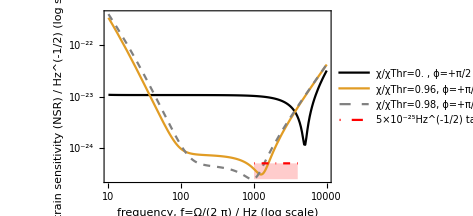

```mathematica
setConfigParamsCustom[2. 10^-6(*m*),4. 10^3(*m*),None, 3 10^6(*W*),None,0.046,400(*kg*),None,2π 500,2π 5000]
plotOptimiseμtricK1[Tla1,Tlb1,Tlc1,Rpd1,False,{1000,4000},0.98]
```